## evolution of curves

### initial curves

#### curves generating function

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];ClearSystemCache[];
```

```mathematica
curgen[num_,width_,height_,kink_,touch_,asymmetrie_,diagonaldistortion_]:=Module[{lo,initialcurve,aoi},
Subscript[te, num,0]=0;
initialcurve[u_]:=Exp[asymmetrie (Sin[u]-1)]({width (1-kink Cos[u]^2)(Sin[u]),height  (1-touch Cos[u]^2)(Cos[u])}+diagonaldistortion{Sin[u],Sin[u]});
aoi=-1/2 NIntegrate[(initialcurve[u][[1]])(D[initialcurve[u][[2]], u])-(initialcurve[u][[2]])( D[initialcurve[u][[1]], u]),{u,0,2π},WorkingPrecision->MachinePrecision];
Subscript[curve, num,0][u_]:=10initialcurve[u]/Sqrt[aoi/(2π)];
Subscript[iao, num]=-1/2 NIntegrate[(Subscript[curve, num,0][u][[1]])(D[Subscript[curve, num,0][u][[2]], u])-(Subscript[curve, num,0][u][[2]])( D[Subscript[curve, num,0][u][[1]], u]),{u,0,2π},WorkingPrecision->MachinePrecision];
ParametricPlot[{Subscript[curve, num,0][u]},{u,0,2π}]];
```

#### curve 1

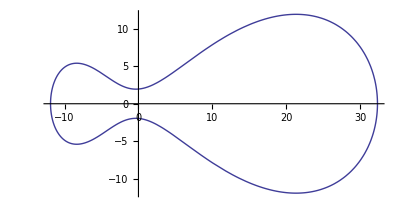

```mathematica
curgen[1,1,1,4/10,9/10,5/10,0]
```

#### curve 2

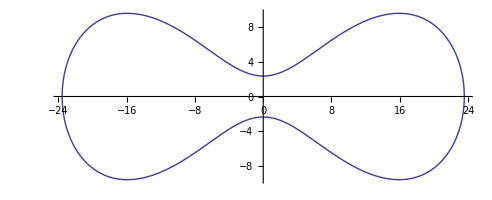

```mathematica
curgen[2,1,1,4/10,9/10,0,0]
```

#### curve 3

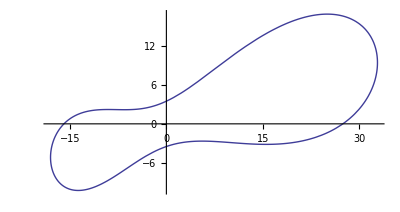

```mathematica
curgen[3,1,1,4/10,8/10,3/10,4/10]
```

#### curve 4

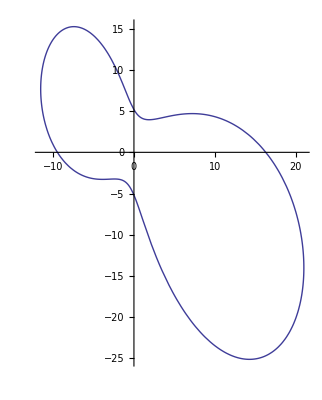

```mathematica
curgen[4,1,1,4/10,8/10,3/10,-4/10]
```

#### curve 5

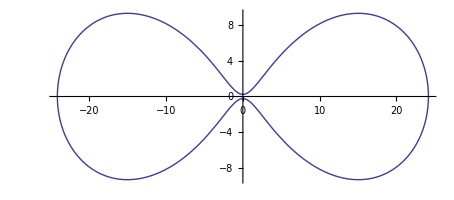

```mathematica
curgen[5,1,1,7/10,99/100,0,0]
```

#### curve 6

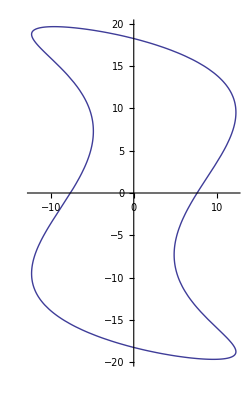

```mathematica
curgen[6,1,15/10,-2,0,0,-6/10]
```

#### curve 7

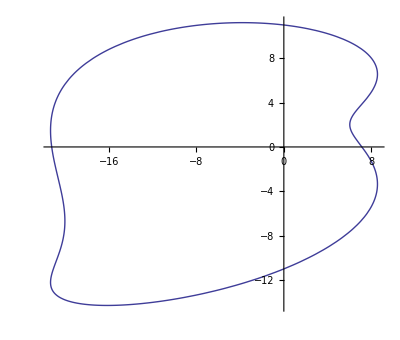

```mathematica
curgen[7,1,1,-2,-1/2,-3/5,1/2]
```

#### curve 8

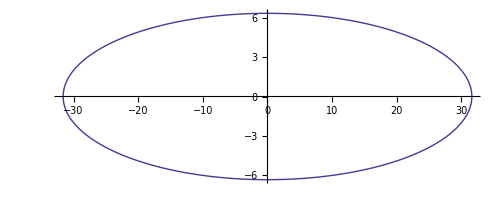

```mathematica
curgen[8,5,1,0,0,0,0]
```

#### curve 9

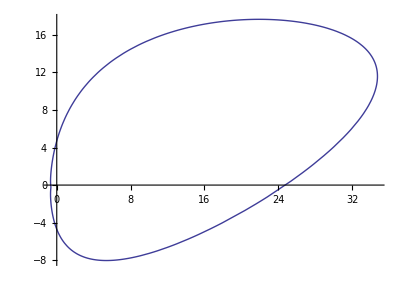

```mathematica
curgen[9,1,1,1/2,-1/2,2,1/2]
```

#### curve 10

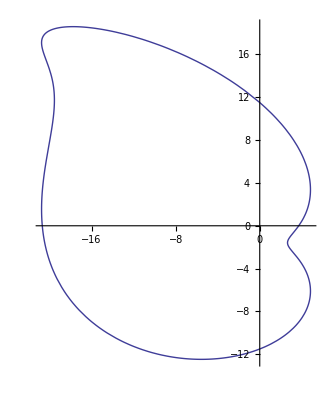

```mathematica
curgen[10,2,1,-1,-1,-1,-3/4]
```

#### curve 11

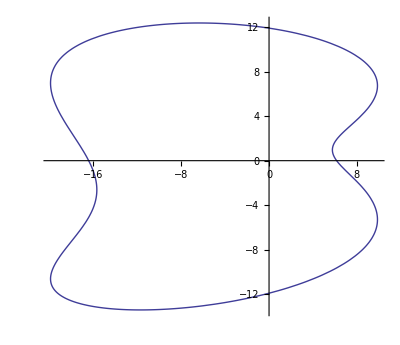

```mathematica
curgen[11,1,1,-25/10,-1/2,-1/2,1/5]
```

#### curve 12

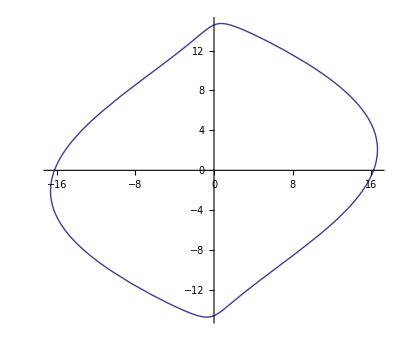

```mathematica
curgen[12, 1, 1,.8,0 ,0,1/7]
```

#### curve 13

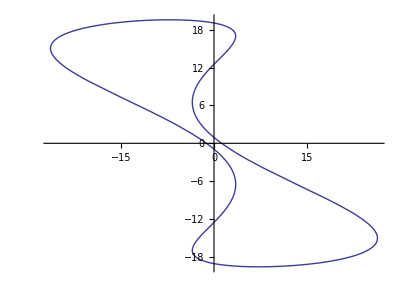

```mathematica
curgen[13, 165/100, .5,1,0 ,0,-6/10]
```

### functions

#### PDE, pbc, length functions

```mathematica
pdeinx =((D[x[u,t], u])^2+(D[y[u,t], u])^2)D[x[u,t], u,u]-(D[x[u,t], u]D[x[u,t], u,u]+D[y[u,t], u]D[y[u,t], u,u])D[x[u,t], u]-((D[x[u,t], u])^2+(D[y[u,t], u])^2)^2 D[x[u,t], t]==0; pdeiny=((D[x[u,t], u])^2+(D[y[u,t], u])^2)D[y[u,t], u,u]-(D[x[u,t], u]D[x[u,t], u,u]+D[y[u,t], u]D[y[u,t], u,u])D[y[u,t], u]-((D[x[u,t], u])^2+(D[y[u,t], u])^2)^2 D[y[u,t], t]==0; 
pbcinx=x[0,t]==x[2π,t] ;
pbciny=y[0,t]==y[2π,t];
clength[num_,step_]:=NIntegrate[Sqrt[(D[Subscript[curve, num,step][u], u]).(D[Subscript[curve, num,step][u], u])],{u,0,2π},MaxRecursion->20,WorkingPrecision->MachinePrecision];slength[num_,step_]:=NIntegrate[Sqrt[(D[x[u,Subscript[te, num,step]], u]/.Subscript[solution, num,step][[1,1]])^2+(D[y[u,Subscript[te, num,step]], u]/.Subscript[solution, num,step][[1,2]])^2],{u,0,2π},MaxRecursion->20,WorkingPrecision->10];
carea[num_,step_]:=-1/2 NIntegrate[(Subscript[curve, num,step][u][[1]])(D[Subscript[curve, num,step][u][[2]], u])-(Subscript[curve, num,step][u][[2]])( D[Subscript[curve, num,step][u][[1]], u]),{u,0,2π},WorkingPrecision->MachinePrecision];
sarea[num_,step_]:=-1/2 NIntegrate[(x[u,Subscript[te, num,step]]/.Subscript[solution, num,step][[1,1]])(D[y[u,Subscript[te, num,step]], u]/.Subscript[solution, num,step][[1,2]])-(y[u,Subscript[te, num,step]]/.Subscript[solution, num,step][[1,2]])( D[x[u,Subscript[te, num,step]], u]/.Subscript[solution, num,step][[1,1]]),{u,0,2π},WorkingPrecision->MachinePrecision]
```

```mathematica
Subscript[solution, 1,1][[1,1]]
```

x→InterpolatingFunction[{{0.,6.28319},{0.,10.}},<>]

#### evolution function

```mathematica
SetOptions[NDSolve`MethodOfLines`TensorProductGrid,MinPoints->100,StartingPoints->100];
flow[num_,step_,tintervall_,opts___]:=Module[{time},
Subscript[te, num,step]=Subscript[te, num,step-1]+tintervall;
Subscript[stepstop, num]=step;
time=Timing[Subscript[solution, num,step]=
NDSolve[{ pdeinx, pdeiny,pbcinx,pbciny,D[pbcinx, t],D[pbciny, t],
x[u,Subscript[te, num,step-1]]==Subscript[curve, num,step-1][u][[1]],
y[u,Subscript[te, num,step-1]]==Subscript[curve, num,step-1][u][[2]]},
{x,y},{u,0,2π},{t,Subscript[te, num,step-1],Subscript[te, num,step]},
DependentVariables->{x,y},
Method->{"MethodOfLines",
"TemporalVariable"->t,
"SpatialDiscretization"->
{"TensorProductGrid",
"DifferenceOrder"->4,
opts},
"DifferentiateBoundaryConditions"->True,
Method->"LinearlyImplicitEuler"},
WorkingPrecision->MachinePrecision,
AccuracyGoal->Automatic,
PrecisionGoal->Automatic,
InterpolationOrder->Automatic,
SolveDelayed->False];];
If[step==1,
Subscript[sl, num,0]=NIntegrate[Sqrt[(D[x[u,0], u]/.Subscript[solution, num,1][[1,1]])^2+(D[y[u,0], u]/.Subscript[solution, num,1][[1,2]])^2],{u,0,2π},WorkingPrecision->MachinePrecision];
Subscript[ao, num]=-1/2 NIntegrate[(x[u,0]/.Subscript[solution, num,1][[1,1]])(D[y[u,0], u]/.Subscript[solution, num,1][[1,2]])-(y[u,0]/.Subscript[solution, num,1][[1,2]])( D[x[u,0], u]/.Subscript[solution, num,1][[1,1]]),{u,0,2π},WorkingPrecision->MachinePrecision];];
Print[num,". curve, ",step,".evolution: initial length = ",clength[num,step-1]," | length after flow = ",
Subscript[sl, num,step]=slength[num,step]," | time of evaluation = ",time[[1]]];
];
fgp[num_,step_,tintervall_,opts___]:=(flow[num,step,tintervall,opts];grdplot[num,step]);
```

#### plotting functions

```mathematica
flowplot[num_,step_]:=ParametricPlot3D[Evaluate[{x[u,t],y[u,t],20t}/. Subscript[solution, num,step]],{u,0,2π},{t,Subscript[te, num,step-1],Subscript[te, num,step]}];
grdplot[num_,step_]:=Module[{xso,yso,grdpts,GridPointPlot},
xso={Subscript[solution, num,step][[1,1]]};
yso={Subscript[solution, num,step][[1,2]]};
GridPointPlot[{x->xif_InterpolatingFunction},{y->yif_InterpolatingFunction}, t_, opts___] := Module[{xgrid = DifferentialEquations`InterpolatingFunctionAnatomy`InterpolatingFunctionCoordinates[xif][[1]]},
ListPlot[Transpose[{ xif[xgrid, t],yif[xgrid, t]}], opts]];
grdpts=
Map[Length,DifferentialEquations`InterpolatingFunctionAnatomy`InterpolatingFunctionCoordinates[x /. xso]][[1]]-1;
Print["gridpoints used by NUMOL: ",grdpts,", endtime from initialcurve = ",Subscript[iao, num]/2/π,", endtime from solution = ",Subscript[ao, num]/2/π];
Show[
ListPlot[Table[Subscript[curve, num,step-1][2Pi/grdpts i],{i,0,(grdpts-1)}],PlotStyle->{Green,Opacity[.5],PointSize[Medium]}],
GridPointPlot[xso,yso,Subscript[te, num,step-1],PlotStyle->{Red,PointSize[Small]}],
GridPointPlot[xso,yso,Subscript[te, num,step],PlotStyle->{Blue,PointSize[Small]}],
PlotLabel->{Style[Subscript["curve", num,step-1],Green],Style[Subscript[" solution", num,step][Subscript[te, num,step-1]],Red],Style[Subscript[" solution", num,step][Subscript[te, num,step]],Blue]}]];
equiplot[num_,step_]:=Show[
ParametricPlot[{{x[u,Subscript[te, num,step]],y[u,Subscript[te, num,step]]}/. Subscript[solution, num,step]},{u,0,2π}],ListPlot[First[{x[u,Subscript[te, num,step]],y[u,Subscript[te, num,step]]}/. Subscript[solution, num,step]]/. Subscript[ulu, num,step],PlotRange->{{-.15,.15},{-.1,.1}}]];
evoplot[num_]:=Block[{stretch=1},
Show[Table[ParametricPlot3D[{Evaluate[{x[u,t],y[u,t],stretch t}/. Subscript[solution, num,i]],{0,0,0}},{u,0,2π},{t,Subscript[te, num,i-1],Subscript[te, num,i]},PlotPoints->{30,10},Mesh->None],{i,Subscript[stepstop, num],1,-1}],PlotRange->All]];
```

#### fitting functions

```mathematica
edp[num_,step_,fitpts_,opts___]:=Module[{length,l,L,usol,time},
Subscript[numberoffitpts, num,step]=fitpts;
length=slength[num,step];
l[i_]:=length i/fitpts;
L[u_?NumberQ]:=NIntegrate[Sqrt[(D[Evaluate[x[p,Subscript[te, num,step]]/.Subscript[solution, num,step][[1,1]]], p])^2+(D[Evaluate[y[p,Subscript[te, num,step]]/.Subscript[solution, num,step][[1,2]]], p])^2],{p,0,u},MaxRecursion->20,opts];
usol[i_]:=FindRoot[L[u]==l[i],{u,0,2Pi},WorkingPrecision->MachinePrecision];
time=Timing[Subscript[ulu, num,step]=Table[usol[i],{i,0,fitpts}]];
Print["u-Bestimmungsdauer: ",time[[1]]];];
fit[num_,step_,order_]:=Module[{fitpts,xpts,ypts,xexp,yexp,xfk,yfk,xpara,ypara,yfitdat,xfitdat,cl,sa,ca},
fitpts=Subscript[numberoffitpts, num,step];
xpts=Table[{2Pi i/fitpts,x[u,Subscript[te, num,step]]/.Subscript[solution, num,step][[1,1]]/.Subscript[ulu, num,step][[i+1]]},{i,0,fitpts}];
ypts=Table[{2Pi i/fitpts,y[u,Subscript[te, num,step]]/.Subscript[solution, num,step][[1,2]]/.Subscript[ulu, num,step][[i+1]]},{i,0,fitpts}];
xexp[u_]:=Sum[Subscript[xfk, i] Cos[i u]+Subscript[xfk, order+i] Sin[i u],{i,0,order}];
yexp[u_]:=Sum[Subscript[yfk, i] Cos[i u]+Subscript[yfk, order+i] Sin[i u],{i,0,order}];
xpara=Table[Subscript[xfk, i] ,{i,0,2 order}];
ypara=Table[Subscript[yfk, i] ,{i,0,2 order}];
xfitdat=FindFit[xpts,xexp[u],xpara ,u];
yfitdat=FindFit[ypts,yexp[u],ypara ,u];
Subscript[curve, num,step][u_]:={xexp[u]/.xfitdat,yexp[u]/.yfitdat};
cl=clength[num,step];
sa=sarea[num,step];
ca=carea[num,step];
Print[num,".curve, ",step,".fit: length unfitted = ",Subscript[sl, num,step]," , length fitted = ",cl," , derivation = ",Abs[Subscript[sl, num,step]-cl]/Subscript[sl, num,step] 100,"%"];
Print["area unfitted = ",sa," , area fitted = ",ca," , derivation = ",Abs[sa-ca]/sa 100,"%"];]
```

#### adaptive flow

```mathematica
aflow[num_,step_,tintervall_,opts___]:=Module[{time},
Subscript[te, num,step]=Subscript[te, num,step-1]+tintervall;
Subscript[stepstop, num]=step;
time=Timing[Subscript[solution, num,step]=
NDSolve[{ pdeinx, pdeiny,pbcinx,pbciny,D[pbcinx, t],D[pbciny, t],
x[u,Subscript[te, num,step-1]]==Evaluate[x[u,Subscript[te, num,step-1]]/.Subscript[solution, num,step-1][[1,1]]],
y[u,Subscript[te, num,step-1]]==Evaluate[y[u,Subscript[te, num,step-1]]/.Subscript[solution, num,step-1][[1,2]]]},
{x,y},{u,0,2π},{t,Subscript[te, num,step-1],Subscript[te, num,step]},
DependentVariables->{x,y},
Method->{"MethodOfLines",
"TemporalVariable"->t,
"SpatialDiscretization"->
{"TensorProductGrid",
"DifferenceOrder"->6,
"Coordinates"->Evaluate[u/. Subscript[ulu, num,step-1]]},
"DifferentiateBoundaryConditions"->True,
Method->Automatic},
WorkingPrecision->MachinePrecision,
AccuracyGoal->Automatic,
PrecisionGoal->Automatic,
InterpolationOrder->Automatic,
SolveDelayed->False];];
Subscript[sl, num,step]=NIntegrate[Sqrt[(D[x[u,Subscript[te, num,step]], u]/.Subscript[solution, num,step][[1,1]])^2+(D[y[u,Subscript[te, num,step]], u]/.Subscript[solution, num,step][[1,2]])^2],{u,0,2π},MaxRecursion->20,WorkingPrecision->10];
Print[num,". curve, ",step,".evolution: initial length = ",Subscript[sl, num,step-1]," | length after flow = ",
Subscript[sl, num,step]," | time of evaluation = ",time[[1]]];
];
agrdplot[num_,step_]:=Module[{xso,yso,grdpts,GridPointPlot},
xso={Subscript[solution, num,step][[1,1]]};
yso={Subscript[solution, num,step][[1,2]]};
GridPointPlot[{x->xif_InterpolatingFunction},{y->yif_InterpolatingFunction}, t_, opts___] := Module[{xgrid = DifferentialEquations`InterpolatingFunctionAnatomy`InterpolatingFunctionCoordinates[xif][[1]]},
ListPlot[Transpose[{ xif[xgrid, t],yif[xgrid, t]}], opts]];
grdpts=
Map[Length,DifferentialEquations`InterpolatingFunctionAnatomy`InterpolatingFunctionCoordinates[x /. xso]][[1]]-1;
Print["gridpoints used by NUMOL: ",grdpts];
Show[
GridPointPlot[xso,yso,Subscript[te, num,step-1],PlotStyle->{Green,PointSize[Small]}],
GridPointPlot[xso,yso,Subscript[te, num,step],PlotStyle->{Blue,PointSize[Small]}],
PlotLabel->{Style[" solution"[Subscript[te, num,step-1]],Green],Style[" solution"[Subscript[te, num,step]],Blue]}]];
afgp[num_,step_,tintervall_,opts___]:=(aflow[num,step,tintervall,opts];agrdplot[num,step]);
```

#### function of coordinates, length, area. plotting functions over entire t

```mathematica
Subscript[xevo, num_][u_,t_]:=Piecewise[Table[{x[u,t]/.Subscript[solution, num,i][[1,1]],Subscript[te, num,i-1]≤t≤Subscript[te, num,i]},{i,1,Subscript[stepstop, num]}],0];
Subscript[yevo, num_][u_,t_]:=Piecewise[Table[{y[u,t]/.Subscript[solution, num,i][[1,2]],Subscript[te, num,i-1]≤t≤Subscript[te, num,i]},{i,1,Subscript[stepstop, num]}],0];
Subscript[length, num_][t_]:=NIntegrate[Sqrt[(D[Subscript[xevo, num][u,t], u])^2+(D[Subscript[yevo, num][u,t], u])^2],{u,0,2π}];
Subscript[area, num_][t_]:=-1/2 NIntegrate[Subscript[xevo, num][u,t] (D[Subscript[yevo, num][u,t], u])-Subscript[yevo, num][u,t]( D[Subscript[xevo, num][u,t], u]),{u,0,2π}];
Subscript[lplot, num_]:=Show[
Plot[{Subscript[length, num][t]},{t,0,Subscript[te, num,Subscript[stepstop, num]]},PlotStyle->Blue],
ListPlot[Table[{Subscript[te, num,i],Subscript[sl, num,i]},{i,0,Subscript[stepstop, num]}],PlotStyle->{PointSize[Large],Green,Opacity[.5]}]];
Subscript[aplot, num_]:=Plot[Subscript[area, num][t],{t,0,Subscript[te, num,Subscript[stepstop, num]]},PlotRange-> Full];
Subscript[isoplot, num_]:=Plot[{Subscript[length, num][t]^2/Subscript[area, num][t],4π},{t,0,Subscript[te, num,Subscript[stepstop, num]]},PlotStyle->Red];
```

### evolution

#### curve 1

1. curve, 1.evolution: initial length = 116.845 | length after flow = 102.7205772 | time of evaluation = 0.612039

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

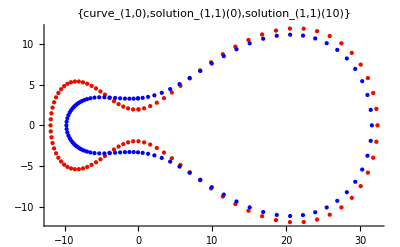

```mathematica
fgp[1,1,10]
```

```mathematica
edp[1,1,10,WorkingPrecision->MachinePrecision,Method->"LocalAdaptive"]
```

u-Bestimmungsdauer: 4.92831

NDSolve::coexp: Because the coordinates were explicitly given for the direction of independent variable u, the values of options {"MaxPoints", "MinPoints", "StartingPoints", "MaxStepSize", "MinStepSize", "StartingStepSize"} will be disregarded for this direction.

1. curve, 2.evolution: initial length = 115.1167285 | length after flow = 106.5383984 | time of evaluation = 0.044003

gridpoints used by NUMOL: 100

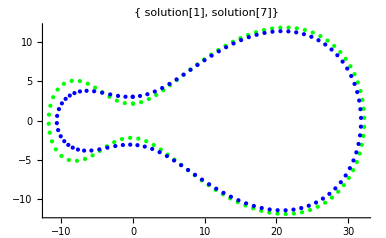

```mathematica
afgp[1,2,6]
```

```mathematica
edp[1,2,100,WorkingPrecision->12]
```

u-Bestimmungsdauer: 39.4985

NDSolve::coexp: Because the coordinates were explicitly given for the direction of independent variable u, the values of options {"MaxPoints", "MinPoints", "StartingPoints", "MaxStepSize", "MinStepSize", "StartingStepSize"} will be disregarded for this direction.

NDSolve::eerri: Warning: Estimated initial error on the specified spatial grid in the direction of independent variable u exceeds prescribed error tolerance.

1. curve, 3.evolution: initial length = 106.5383984 | length after flow = 105.2499838 | time of evaluation = 0.032002

gridpoints used by NUMOL: 100

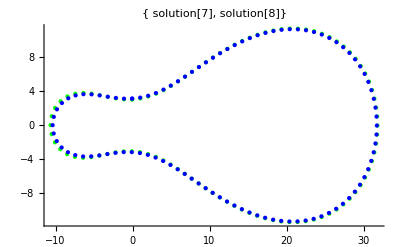

```mathematica
afgp[1,3,1]
```

```mathematica
fit[1,1,19];
```

1.curve, 1.fit: length unfitted = 88.1165 , length fitted = 88.1159 , derivation = 0.000610623%

area unfitted = 489.88 , area fitted = 489.878 , derivation = 0.000250471%

1. curve, 2.evolution: initial length = 88.1159 | length after flow = 55.58251941338 | time of evaluation = 2.58016

gridpoints used by NUMOL: 130, endtime from initialcurve = 100., endtime from solution = 100.

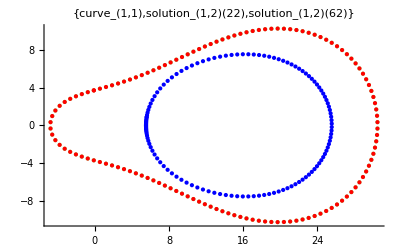

```mathematica
fgp[1,2,40]
```

```mathematica
edp[1,2,5,WorkingPrecision->MachinePrecision];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: "slwcon" will be suppressed during this calculation.

u-Bestimmungsdauer: 6.95243

```mathematica
fit[1,2,3]
```

1. curve, 2. fit: length after flow = 8.17051 , length after fit = 8.17053 , derivation = 0.000226096 %

1. curve, 3.evolution: initial length = 8.17053 | length after flow = 1.50319 | time of evaluation = 0.16401

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

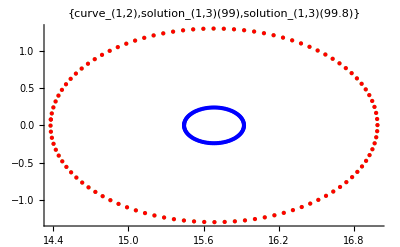

```mathematica
fgp[1,3,.8]
```

```mathematica
edp[1,3,40]
```

u-Bestimmungsdauer: 12.9248

```mathematica
fit[1,3,2]
```

1. curve, 3. fit: length after flow = 1.50319 , length after fit = 1.50319 , derivation = 0.0000888977 %

1. curve, 4.evolution: initial length = 1.50319 | length after flow = 0.382915 | time of evaluation = 0.092005

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

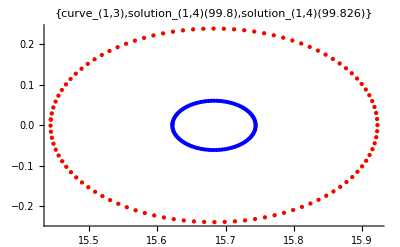

```mathematica
fgp[1,4,.026]
```

```mathematica
edp[1,4,40];
```

u-Bestimmungsdauer: 12.2008

```mathematica
fit[1,4,1]
```

1. curve, 4. fit: length after flow = 0.382915 , length after fit = 0.382915 , derivation = 0.0000673811 %

1. curve, 5.evolution: initial length = 0.382915 | length after flow = 0.123144 | time of evaluation = 0.068004

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

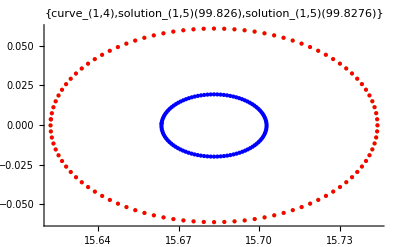

```mathematica
fgp[1,5,.0016]
```

```mathematica
edp[1,5,40]
```

u-Bestimmungsdauer: 12.4568

```mathematica
fit[1,5,1]
```

1. curve, 5. fit: length after flow = 0.0677695 , length after fit = 0.0677695 , derivation = 0.0000218348 %

1. curve, 6.evolution: initial length = 0.0677695 | length after flow = 0.0222643 | time of evaluation = 0.064004

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

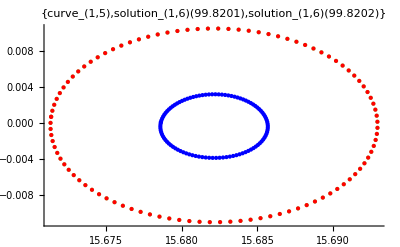

```mathematica
fgp[1,6,.00005]
```

```mathematica
evoplot[1]
```

-Graphics3D-

```mathematica
edp[1,6,40]
```

u-Bestimmungsdauer: 13.4128

```mathematica
fit[1,6,1]
```

1. curve, 6. fit: length after flow = 0.0222643 , length after fit = 0.0222634 , derivation = 0.00412316 %

```mathematica
fgp[1,7,.000219]
```

fgp[1,7,0.000219]

```mathematica
edp[1,7,32]
```

edp[1,7,32]

```mathematica
fit[1,7,1]
```

fit[1,7,1]

```mathematica
fgp[1,8,.00000705]
```

fgp[1,8,7.05×10^-6]

#### curve 2

2. curve, 1.evolution: initial length = 125.675 | length after flow = 28.4168 | time of evaluation = 2.04813

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

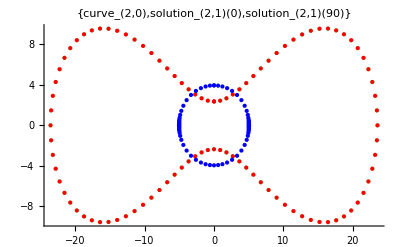

```mathematica
fgp[2,1,90]
```

```mathematica
edp[2,1,100]
```

u-Bestimmungsdauer: 112.943

```mathematica
fit[2,1,5]
```

2. curve, 1. fit: length after flow = 28.4168 , length after fit = 28.4167 , derivation = 0.0000941926 %

2. curve, 2.evolution: initial length = 28.4167 | length after flow = 0.998398 | time of evaluation = 0.172011

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

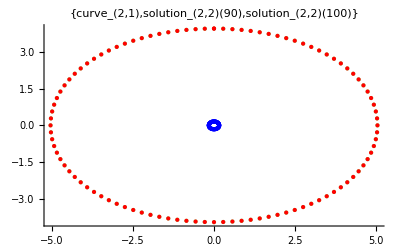

```mathematica
fgp[2,2,10]
```

```mathematica
edp[2,2,50];
```

u-Bestimmungsdauer: 20.5173

```mathematica
fit[2,2,3]
```

2. curve, 2. fit: length after flow = 0.998398 , length after fit = 0.998397 , derivation = 0.00001283 %

2. curve, 3.evolution: initial length = 0.998397 | length after flow = 0.723218 | time of evaluation = 0.064003

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

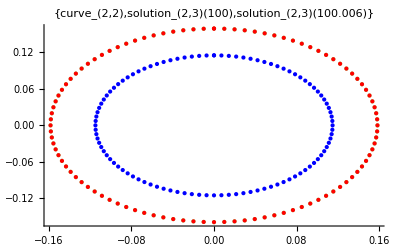

```mathematica
fgp[2,3,.006]
```

```mathematica
edp[2,3,40];
```

u-Bestimmungsdauer: 19.5772

```mathematica
fit[2,3,3];
```

2. curve, 3. fit: length after flow = 0.987509 , length after fit = 0.987509 , derivation = 4.63578×10^-7 %

2. curve, 4.evolution:   initial length = 0.987509 , length after flow = 0.102379 , time of evaluation = 0.064004

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999996

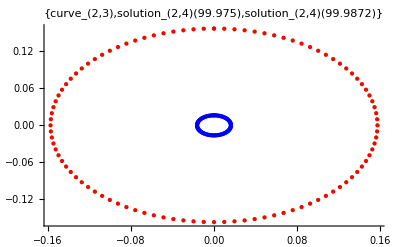

```mathematica
fgp[2,4,.01215]
```

```mathematica
edp[2,4,40]
```

u-Bestimmungsdauer: 13.8169

```mathematica
fit[2,4,1]
```

2. curve, 4. fit: length after flow = 0.102379 , length after fit = 0.102379 , derivation = 0.0000590925 %

2. curve, 5.evolution:   initial length = 0.102379 , length after flow = 0.024146 , time of evaluation = 0.052003

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999996

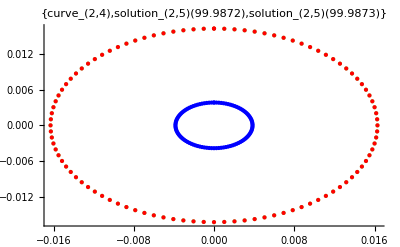

```mathematica
fgp[2,5,.000122]
```

```mathematica
edp[2,5,20]
```

u-Bestimmungsdauer: 6.30039

```mathematica
fit[2,5,1]
```

2. curve, 5. fit: length after flow = 0.024146 , length after fit = 0.024146 , derivation = 2.34105×10^-7 %

2. curve, 6.evolution:   initial length = 0.024146 , length after flow = 0.00889205 , time of evaluation = 0.032002

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999996

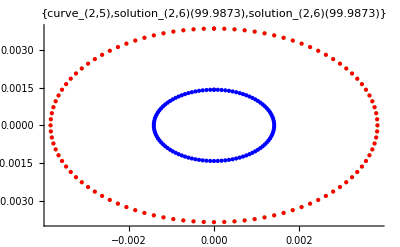

```mathematica
fgp[2,6,.0000063]
```

#### curve 3

3. curve, 1.evolution:   initial length = 125.655 , length after flow = 86.0262 , time of evaluation = 0.440027

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999622

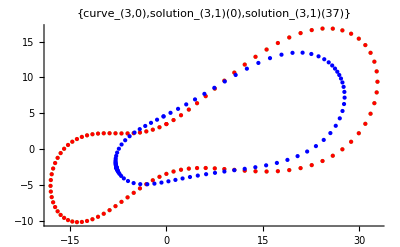

```mathematica
fgp[3,1,37]
```

```mathematica
edp[3,1,120]
```

u-Bestimmungsdauer: 56.3675

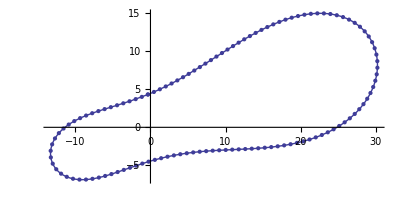

```mathematica
equiplot[3,1]
```

```mathematica
fit[3,1,20]
```

3. curve, 1. fit: length after flow = 104.18 , length after fit = 104.18 , derivation = 0.0000583601 %

NDSolve::eerr: Warning: Scaled local spatial error estimate of 12.7461 at t = 45.7 in the direction of independent variable u is much greater than prescribed error tolerance. Grid spacing with 101 points may be too large to achieve the desired accuracy or precision.  A singularity may have formed or you may want to specify a smaller grid spacing using the MaxStepSize or MinPoints method options.

3. curve, 2.evolution:   initial length = 104.18 , length after flow = 76.4223 , time of evaluation = 0.728046

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999622

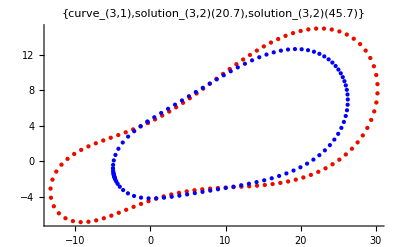

```mathematica
fgp[3,2,25]
```

```mathematica
edp[3,2,120]
```

u-Bestimmungsdauer: 63.936

```mathematica
fit[3,2,18]
```

3. curve, 2. fit: length after flow = 82.1534 , length after fit = 82.1533 , derivation = 0.000100781 %

NDSolve::eerr: Warning: Scaled local spatial error estimate of 117.53 at t = 60. in the direction of independent variable u is much greater than prescribed error tolerance. Grid spacing with 101 points may be too large to achieve the desired accuracy or precision.  A singularity may have formed or you may want to specify a smaller grid spacing using the MaxStepSize or MinPoints method options.

3. curve, 3.evolution:   initial length = 82.1533 , length after flow = 61.6479 , time of evaluation = 0.140009

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999622

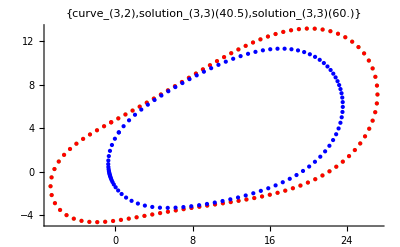

```mathematica
fgp[3,3,19.5]
```

```mathematica
edp[3,3,100]
```

u-Bestimmungsdauer: 55.7835

```mathematica
fit[3,3,12]
```

3. curve, 3. fit: length after flow = 61.6479 , length after fit = 61.6479 , derivation = 0.0000248322 %

3. curve, 4.evolution:   initial length = 61.6479 , length after flow = 39.1076 , time of evaluation = 0.096005

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999622

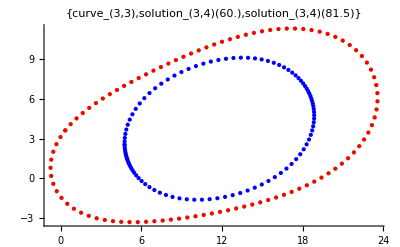

```mathematica
fgp[3,4,21.5]
```

```mathematica
edp[3,4,80]
```

u-Bestimmungsdauer: 42.7267

```mathematica
fit[3,4,5]
```

3. curve, 4. fit: length after flow = 39.1076 , length after fit = 39.1077 , derivation = 0.0000904822 %

NDSolve::eerr: Warning: Scaled local spatial error estimate of 208.31 at t = 98.7 in the direction of independent variable u is much greater than prescribed error tolerance. Grid spacing with 101 points may be too large to achieve the desired accuracy or precision.  A singularity may have formed or you may want to specify a smaller grid spacing using the MaxStepSize or MinPoints method options.

3. curve, 5.evolution:   initial length = 39.1077 , length after flow = 10.1069 , time of evaluation = 0.088006

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999622

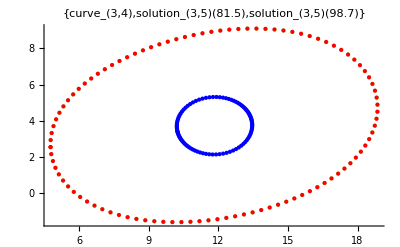

```mathematica
fgp[3,5,17.2]
```

```mathematica
edp[3,5,60]
```

u-Bestimmungsdauer: 30.7459

```mathematica
fit[3,5,3]
```

3. curve, 5. fit: length after flow = 10.1069 , length after fit = 10.1069 , derivation = 0.000379432 %

NDSolve::eerr: Warning: Scaled local spatial error estimate of 13.4122 at t = 99.708 in the direction of independent variable u is much greater than prescribed error tolerance. Grid spacing with 101 points may be too large to achieve the desired accuracy or precision.  A singularity may have formed or you may want to specify a smaller grid spacing using the MaxStepSize or MinPoints method options.

3. curve, 6.evolution:   initial length = 10.1069 , length after flow = 4.73048 , time of evaluation = 0.032002

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999622

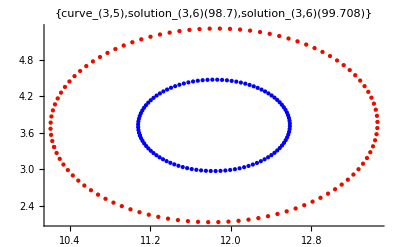

```mathematica
fgp[3,6,1.008]
```

```mathematica
edp[3,6,50]
```

u-Bestimmungsdauer: 18.6212

```mathematica
fit[3,6,3]
```

3. curve, 6. fit: length after flow = 4.73048 , length after fit = 4.73049 , derivation = 0.000178842 %

NDSolve::eerr: Warning: Scaled local spatial error estimate of 40.7099 at t = 99.921 in the direction of independent variable u is much greater than prescribed error tolerance. Grid spacing with 101 points may be too large to achieve the desired accuracy or precision.  A singularity may have formed or you may want to specify a smaller grid spacing using the MaxStepSize or MinPoints method options.

3. curve, 7.evolution:   initial length = 4.73049 , length after flow = 2.34712 , time of evaluation = 0.032002

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999622

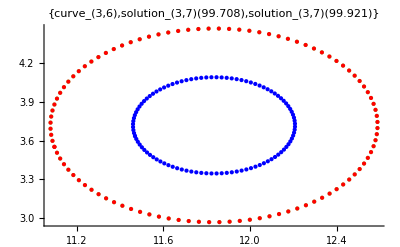

```mathematica
fgp[3,7,.213]
```

```mathematica
edp[3,7,40]
```

u-Bestimmungsdauer: 13.3928

```mathematica
fit[3,7,3]
```

3. curve, 7. fit: length after flow = 2.34712 , length after fit = 2.34712 , derivation = 0.000239184 %

3. curve, 8.evolution:   initial length = 2.34712 , length after flow = 1.1407 , time of evaluation = 0.024002

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999622

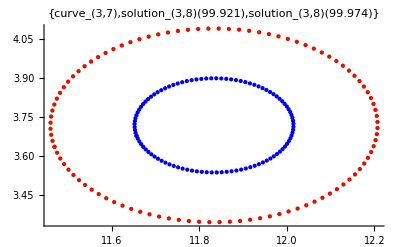

```mathematica
fgp[3,8,.053]
```

```mathematica
edp[3,8,40]
```

u-Bestimmungsdauer: 13.2088

```mathematica
fit[3,8,3]
```

3. curve, 8. fit: length after flow = 1.1407 , length after fit = 1.1407 , derivation = 9.98047×10^-8 %

NDSolve::eerr: Warning: Scaled local spatial error estimate of 1.38273×10^6 at t = 100.008 in the direction of independent variable u is much greater than prescribed error tolerance. Grid spacing with 101 points may be too large to achieve the desired accuracy or precision.  A singularity may have formed or you may want to specify a smaller grid spacing using the MaxStepSize or MinPoints method options.

3. curve, 9.evolution:   initial length = 1.1407 , length after flow = 0.0616066 , time of evaluation = 3.67223

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999622

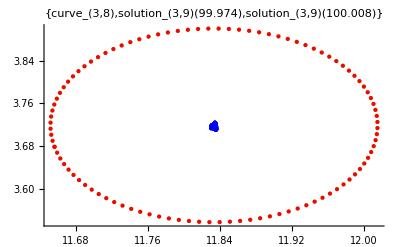

```mathematica
fgp[3,9,.034]
```

```mathematica
edp[3,9,36]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: "slwcon" will be suppressed during this calculation.

u-Bestimmungsdauer: 107.475

```mathematica
fit[3,9,1]
```

3. curve, 9. fit: length after flow = 0.0616066 , length after fit = 0.0236954 , derivation = 61.5376 %

NDSolve::eerr: Warning: Scaled local spatial error estimate of 3.58538×10^6 at t = 100.008 in the direction of independent variable u is much greater than prescribed error tolerance. Grid spacing with 101 points may be too large to achieve the desired accuracy or precision.  A singularity may have formed or you may want to specify a smaller grid spacing using the MaxStepSize or MinPoints method options.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

3. curve, 10.evolution:   initial length = 0.0236954 , length after flow = 0.0402141 , time of evaluation = 3.2642

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999622

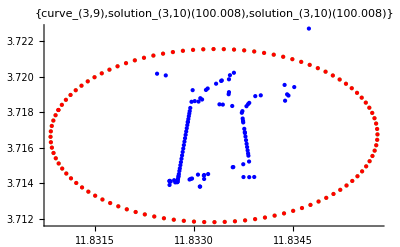

```mathematica
fgp[3,10,.0002]
```

```mathematica
edp[3,10,36]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: "slwcon" will be suppressed during this calculation.

u-Bestimmungsdauer: 88.5055

```mathematica
fit[3,10,1]
```

3. curve, 10. fit: length after flow = 0.0402141 , length after fit = 0.014417 , derivation = 64.1495 %

NDSolve::eerr: Warning: Scaled local spatial error estimate of 8.0581×10^6 at t = 100.008 in the direction of independent variable u is much greater than prescribed error tolerance. Grid spacing with 101 points may be too large to achieve the desired accuracy or precision.  A singularity may have formed or you may want to specify a smaller grid spacing using the MaxStepSize or MinPoints method options.

3. curve, 11.evolution:   initial length = 0.014417 , length after flow = 0.0590321 , time of evaluation = 1.6041

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999622

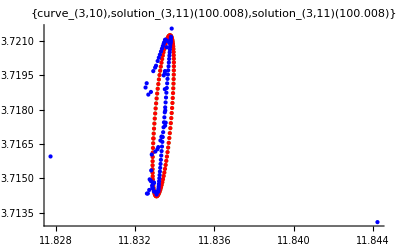

```mathematica
fgp[3,11,.0000232]
```

```mathematica
edp[3,11,32]
```

$Aborted

```mathematica
fit[3,11,2]
```

3. curve, 11. fit: length after flow = 0.171856 , length after fit = 0.171856 , derivation = 1.834×10^-6 %

3. curve, 12.evolution:   initial length = 0.171856 , length after flow = 0.17128 , time of evaluation = 0.020001

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999997

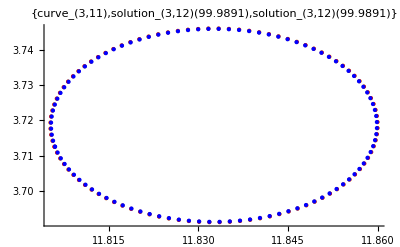

```mathematica
fgp[3,12,.0000025]
```

```mathematica
edp[3,12,32]
```

u-Bestimmungsdauer: 8.49653

```mathematica
fit[3,12,1]
```

3. curve, 12. fit: length after flow = 0.17128 , length after fit = 0.17128 , derivation = 1.50898×10^-6 %

3. curve, 13.evolution:   initial length = 0.17128 , length after flow = 0.170933 , time of evaluation = 0.012001

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999997

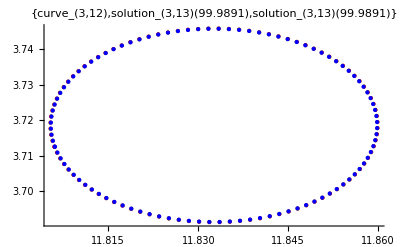

```mathematica
fgp[3,13,.000001505]
```

#### curve 4

4. curve, 1.evolution:   initial length = 115.761 , length after flow = 78.9025 , time of evaluation = 0.132008

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.9999999

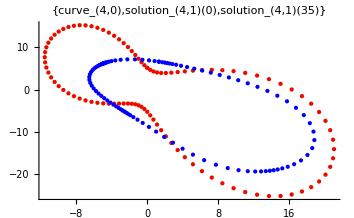

```mathematica
fgp[4,1,35]
```

```mathematica
edp[4,1,100]
```

u-Bestimmungsdauer: 79.225

```mathematica
fit[4,1,12]
```

4. curve, 1. fit: length after flow = 78.9025 , length after fit = 78.9025 , derivation = 0.0000290521 %

4. curve, 2.evolution:   initial length = 78.9025 , length after flow = 32.1812 , time of evaluation = 0.140009

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.9999999

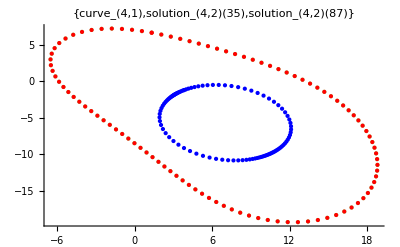

```mathematica
fgp[4,2,52]
```

```mathematica
edp[4,2,60]
```

u-Bestimmungsdauer: 44.2988

```mathematica
fit[4,2,13]
```

4. curve, 2. fit: length after flow = 32.1812 , length after fit = 32.1812 , derivation = 0.0000862097 %

4. curve, 3.evolution:   initial length = 32.1812 , length after flow = 1.983 , time of evaluation = 0.112007

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.9999999

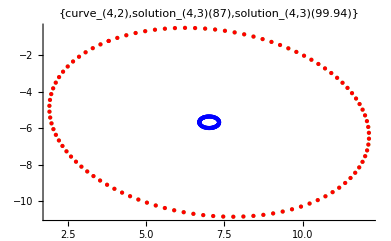

```mathematica
fgp[4,3,12.94]
```

```mathematica
edp[4,3,40]
```

u-Bestimmungsdauer: 20.5933

```mathematica
fit[4,3,3]
```

4. curve, 3. fit: length after flow = 1.983 , length after fit = 1.983 , derivation = 0.000115039 %

4. curve, 4.evolution:   initial length = 1.983 , length after flow = 0.383752 , time of evaluation = 0.060003

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.9999999

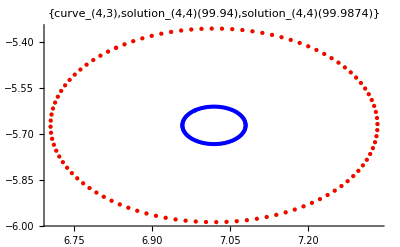

```mathematica
fgp[4,4,.0474]
```

```mathematica
edp[4,4,40]
```

u-Bestimmungsdauer: 14.5649

```mathematica
fit[4,4,1]
```

4. curve, 4. fit: length after flow = 0.383752 , length after fit = 0.383752 , derivation = 0.0000403996 %

4. curve, 5.evolution:   initial length = 0.383752 , length after flow = 0.214431 , time of evaluation = 0.036002

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.9999999

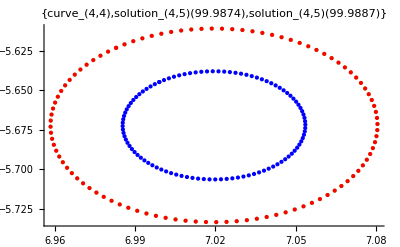

```mathematica
fgp[4,5,.00127]
```

```mathematica
edp[4,5,24]
```

u-Bestimmungsdauer: 7.82049

```mathematica
fit[4,5,1]
```

4. curve, 5. fit: length after flow = 0.214431 , length after fit = 0.214431 , derivation = 0.0000307918 %

4. curve, 6.evolution:   initial length = 0.214431 , length after flow = 0.071662 , time of evaluation = 0.024001

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.9999999

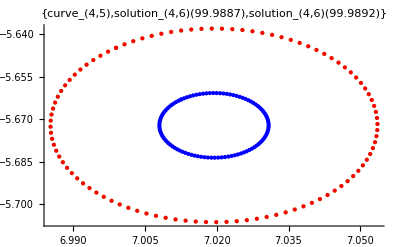

```mathematica
fgp[4,6,.00051]
```

```mathematica
edp[4,6,24]
```

u-Bestimmungsdauer: 7.56847

```mathematica
fit[4,6,1]
```

4. curve, 6. fit: length after flow = 0.071662 , length after fit = 0.071662 , derivation = 0.0000797768 %

4. curve, 7.evolution:   initial length = 0.071662 , length after flow = 0.0298145 , time of evaluation = 0.044003

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.9999999

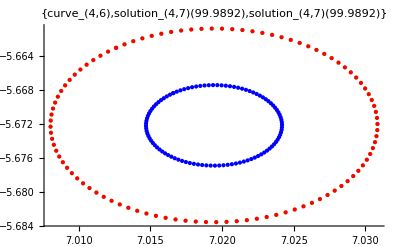

```mathematica
fgp[4,7,.000052]
```

#### curve 5

5. curve, 1.evolution:   initial length = 130.819 , length after flow = 28.4642 , time of evaluation = 0.168011

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999992

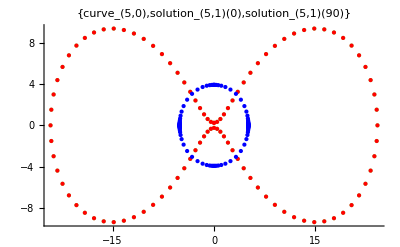

```mathematica
fgp[5,1,90]
```

```mathematica
edp[5,1,80]
```

u-Bestimmungsdauer: 81.7851

```mathematica
fit[5,1,8]
```

5. curve, 1. fit: length after flow = 28.4642 , length after fit = 28.4642 , derivation = 0.00004229 %

5. curve, 2.evolution:   initial length = 28.4642 , length after flow = 7.41121 , time of evaluation = 0.076005

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999992

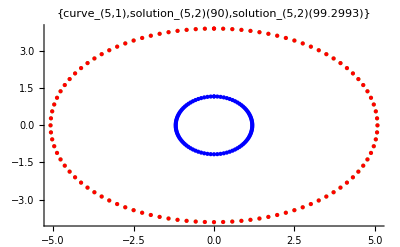

```mathematica
fgp[5,2,9.2993]
```

```mathematica
edp[5,2,40]
```

u-Bestimmungsdauer: 19.4292

```mathematica
fit[5,2,3]
```

5. curve, 2. fit: length after flow = 7.41121 , length after fit = 7.41121 , derivation = 0.0000245108 %

5. curve, 3.evolution:   initial length = 7.41121 , length after flow = 1.12473 , time of evaluation = 0.064004

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999992

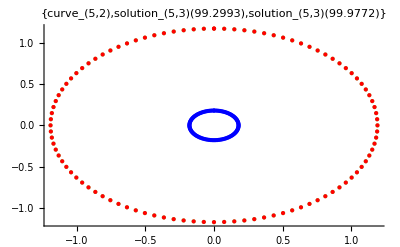

```mathematica
fgp[5,3,.677901]
```

```mathematica
edp[5,3,20]
```

u-Bestimmungsdauer: 8.34452

```mathematica
fit[5,3,3]
```

5. curve, 3. fit: length after flow = 1.12473 , length after fit = 1.12473 , derivation = 0.000011387 %

5. curve, 4.evolution:   initial length = 1.12473 , length after flow = 0.508328 , time of evaluation = 0.040003

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999992

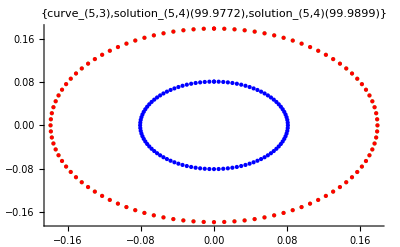

```mathematica
fgp[5,4,.0126999]
```

```mathematica
edp[5,4,20]
```

u-Bestimmungsdauer: 7.18045

```mathematica
fit[5,4,1]
```

5. curve, 4. fit: length after flow = 0.508328 , length after fit = 0.508328 , derivation = 0.0000363034 %

5. curve, 5.evolution:   initial length = 0.508328 , length after flow = 0.0287676 , time of evaluation = 0.072004

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999992

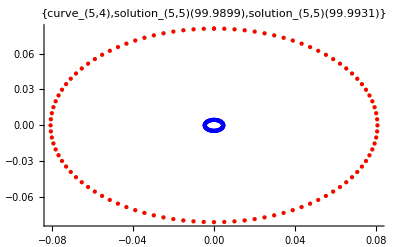

```mathematica
fgp[5,5,.00322]
```

#### curve 6

6. curve, 1.evolution:   initial length = 123.348 , length after flow = 119.835 , time of evaluation = 0.028001

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

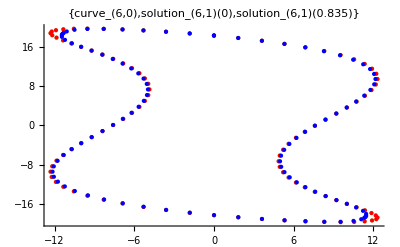

```mathematica
fgp[6,1,.835]
```

```mathematica
edp[6,1,100]
```

u-Bestimmungsdauer: 51.6672

```mathematica
fit[6,1,18]
```

6. curve, 1. fit: length after flow = 119.835 , length after fit = 119.418 , derivation = 0.347842 %

6. curve, 2.evolution:   initial length = 119.418 , length after flow = 113.078 , time of evaluation = 0.080005

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

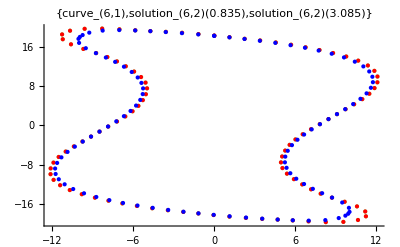

```mathematica
fgp[6,2,2.25]
```

```mathematica
edp[6,2,100]
```

u-Bestimmungsdauer: 45.9949

```mathematica
fit[6,2,15]
```

6. curve, 2. fit: length after flow = 113.078 , length after fit = 112.91 , derivation = 0.148444 %

6. curve, 3.evolution:   initial length = 112.91 , length after flow = 71.7333 , time of evaluation = 0.168011

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

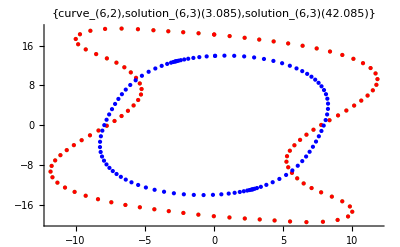

```mathematica
fgp[6,3,39]
```

```mathematica
edp[6,3,80]
```

u-Bestimmungsdauer: 55.3035

```mathematica
fit[6,3,10]
```

6. curve, 3. fit: length after flow = 71.7333 , length after fit = 71.7316 , derivation = 0.00243305 %

6. curve, 4.evolution:   initial length = 71.7316 , length after flow = 26.8704 , time of evaluation = 0.100006

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

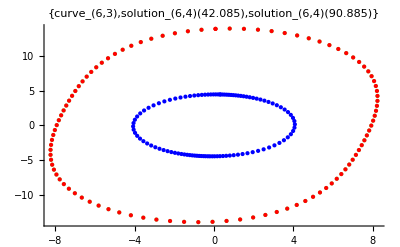

```mathematica
fgp[6,4,48.8]
```

```mathematica
edp[6,4,50]
```

u-Bestimmungsdauer: 30.8379

```mathematica
fit[6,4,3]
```

6. curve, 4. fit: length after flow = 26.8704 , length after fit = 26.8705 , derivation = 0.000436305 %

6. curve, 5.evolution:   initial length = 26.8705 , length after flow = 9.33108 , time of evaluation = 0.060003

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

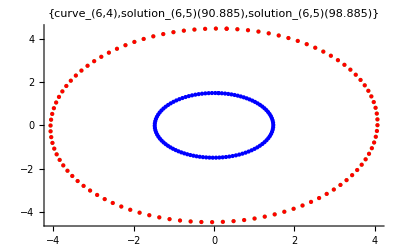

```mathematica
fgp[6,5,8.]
```

```mathematica
edp[6,5,40]
```

u-Bestimmungsdauer: 18.6372

```mathematica
fit[6,5,3]
```

6. curve, 5. fit: length after flow = 9.33108 , length after fit = 9.33108 , derivation = 0.0000285344 %

NDSolve::eerr: Warning: Scaled local spatial error estimate of 73.4825 at t = 99.915 in the direction of independent variable u is much greater than prescribed error tolerance. Grid spacing with 101 points may be too large to achieve the desired accuracy or precision.  A singularity may have formed or you may want to specify a smaller grid spacing using the MaxStepSize or MinPoints method options.

6. curve, 6.evolution:   initial length = 9.33108 , length after flow = 2.3651 , time of evaluation = 0.064004

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

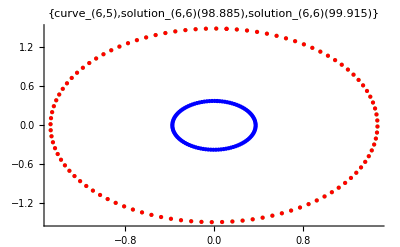

```mathematica
fgp[6,6,1.03]
```

```mathematica
edp[6,6,28]
```

u-Bestimmungsdauer: 12.1688

```mathematica
fit[6,6,3]
```

6. curve, 6. fit: length after flow = 2.3651 , length after fit = 2.36511 , derivation = 0.0000861004 %

6. curve, 7.evolution:   initial length = 2.36511 , length after flow = 0.934113 , time of evaluation = 0.048003

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

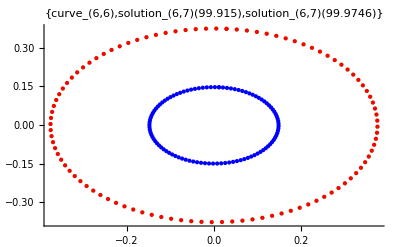

```mathematica
fgp[6,7,.05963]
```

```mathematica
edp[6,7,28]
```

u-Bestimmungsdauer: 10.8647

```mathematica
fit[6,7,3]
```

6. curve, 7. fit: length after flow = 0.934113 , length after fit = 0.934115 , derivation = 0.000196327 %

6. curve, 8.evolution:   initial length = 0.934115 , length after flow = 0.471307 , time of evaluation = 0.040003

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

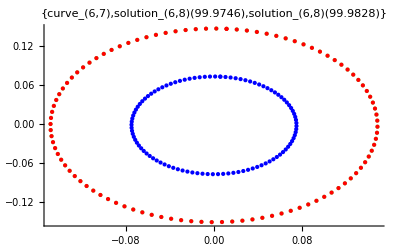

```mathematica
fgp[6,8,.0082]
```

```mathematica
edp[6,8,24]
```

u-Bestimmungsdauer: 7.59647

```mathematica
fit[6,8,3]
```

6. curve, 8. fit: length after flow = 0.471307 , length after fit = 0.471307 , derivation = 6.91969×10^-8 %

6. curve, 9.evolution:   initial length = 0.471307 , length after flow = 0.148811 , time of evaluation = 0.052003

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

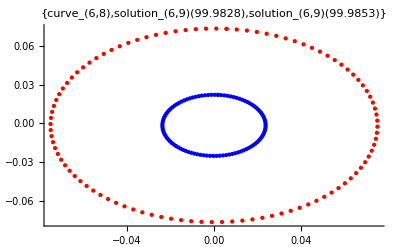

```mathematica
fgp[6,9,.00251]
```

```mathematica
edp[6,9,24]
```

u-Bestimmungsdauer: 7.9245

```mathematica
fit[6,9,1]
```

6. curve, 9. fit: length after flow = 0.148811 , length after fit = 0.148811 , derivation = 1.43251×10^-6 %

6. curve, 10.evolution:   initial length = 0.148811 , length after flow = 0.146539 , time of evaluation = 0.024002

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

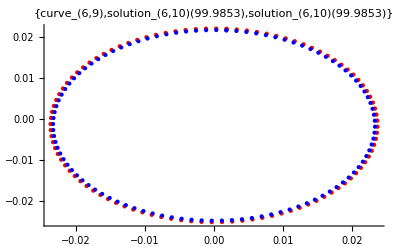

```mathematica
fgp[6,10,.0000085]
```

#### curve 7

7. curve, 1.evolution:   initial length = 96.4821 , length after flow = 75.4053 , time of evaluation = 0.088005

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999998

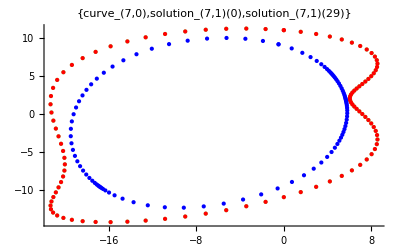

```mathematica
fgp[7,1,29]
```

```mathematica
edp[7,1,80]
```

u-Bestimmungsdauer: 70.6324

```mathematica
fit[7,1,10]
```

7. curve, 1. fit: length after flow = 75.4053 , length after fit = 75.4053 , derivation = 6.67354×10^-6 %

7. curve, 2.evolution:   initial length = 75.4053 , length after flow = 8.77111 , time of evaluation = 0.096006

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999998

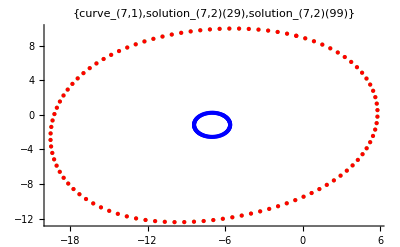

```mathematica
fgp[7,2,70]
```

```mathematica
edp[7,2,40]
```

u-Bestimmungsdauer: 22.4654

```mathematica
fit[7,2,3]
```

7. curve, 2. fit: length after flow = 8.77111 , length after fit = 8.77111 , derivation = 4.11093×10^-7 %

7. curve, 3.evolution:   initial length = 8.77111 , length after flow = 1.18479 , time of evaluation = 0.072004

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999998

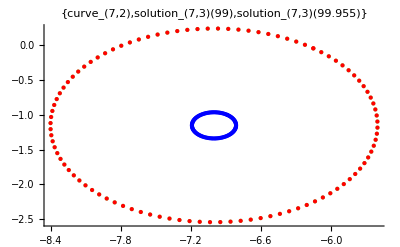

```mathematica
fgp[7,3,.955]
```

```mathematica
edp[7,3,40]
```

u-Bestimmungsdauer: 15.425

```mathematica
fit[7,3,2]
```

7. curve, 3. fit: length after flow = 1.18479 , length after fit = 1.18479 , derivation = 8.15246×10^-6 %

7. curve, 4.evolution:   initial length = 1.18479 , length after flow = 0.576461 , time of evaluation = 0.048003

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999998

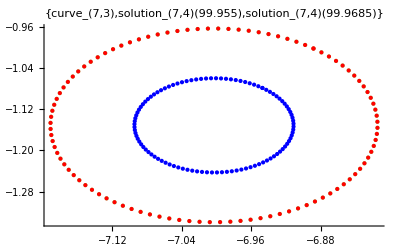

```mathematica
fgp[7,4,.0135]
```

```mathematica
edp[7,4,20]
```

u-Bestimmungsdauer: 6.3764

```mathematica
fit[7,4,1]
```

7. curve, 4. fit: length after flow = 0.576461 , length after fit = 0.576462 , derivation = 0.0002062 %

7. curve, 5.evolution:   initial length = 0.576462 , length after flow = 0.101783 , time of evaluation = 0.056004

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999998

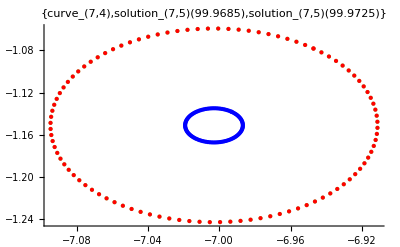

```mathematica
fgp[7,5,.00403]
```

```mathematica
edp[7,5,20]
```

u-Bestimmungsdauer: 6.3124

```mathematica
fit[7,5,1]
```

7. curve, 5. fit: length after flow = 0.101783 , length after fit = 0.101783 , derivation = 0.000199056 %

7. curve, 6.evolution:   initial length = 0.101783 , length after flow = 0.0644006 , time of evaluation = 0.036003

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999998

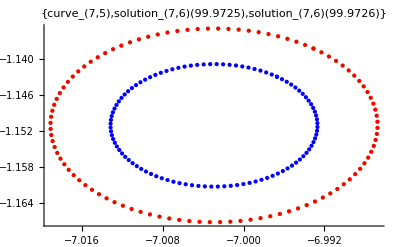

```mathematica
fgp[7,6,.000078]
```

```mathematica
edp[7,6,20]
```

u-Bestimmungsdauer: 6.77642

```mathematica
fit[7,6,1]
```

7. curve, 6. fit: length after flow = 0.0644006 , length after fit = 0.0644006 , derivation = 0.0000287544 %

7. curve, 7.evolution:   initial length = 0.0644006 , length after flow = 0.0442797 , time of evaluation = 0.040002

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999998

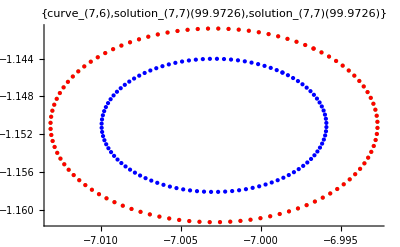

```mathematica
fgp[7,7,.0000275]
```

```mathematica
edp[7,7,20]
```

u-Bestimmungsdauer: 6.16039

```mathematica
fit[7,7,1]
```

7. curve, 7. fit: length after flow = 0.0442797 , length after fit = 0.0442797 , derivation = 3.27851×10^-6 %

7. curve, 8.evolution:   initial length = 0.0442797 , length after flow = 0.0164459 , time of evaluation = 0.032002

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999998

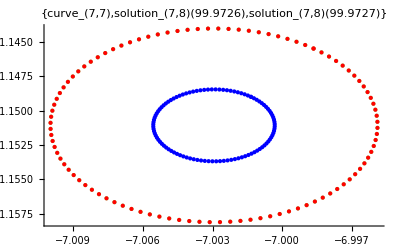

```mathematica
fgp[7,8,.0000211]
```

#### curve 8

8. curve, 1.evolution:   initial length = 132.879 , length after flow = 108.054 , time of evaluation = 0.108006

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

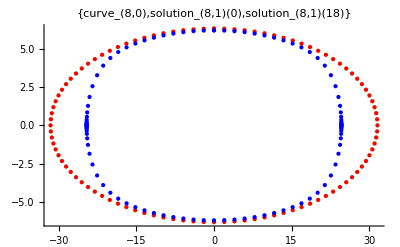

```mathematica
fgp[8,1,18]
```

```mathematica
edp[8,1,100]
```

u-Bestimmungsdauer: 77.6889

```mathematica
fit[8,1,20]
```

8. curve, 1. fit: length after flow = 108.054 , length after fit = 108.054 , derivation = 0.000417457 %

8. curve, 2.evolution:   initial length = 108.054 , length after flow = 62.7697 , time of evaluation = 0.16401

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

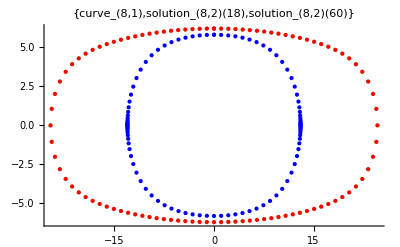

```mathematica
fgp[8,2,42]
```

```mathematica
edp[8,2,80]
```

u-Bestimmungsdauer: 62.3999

```mathematica
fit[8,2,9]
```

8. curve, 2. fit: length after flow = 62.7697 , length after fit = 62.7697 , derivation = 0.000120993 %

8. curve, 3.evolution:   initial length = 62.7697 , length after flow = 25.2929 , time of evaluation = 0.096006

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

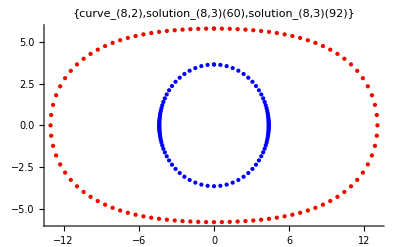

```mathematica
fgp[8,3,32]
```

```mathematica
edp[8,3,60]
```

u-Bestimmungsdauer: 38.5424

```mathematica
fit[8,3,5]
```

8. curve, 3. fit: length after flow = 25.2929 , length after fit = 25.2929 , derivation = 8.67901×10^-6 %

8. curve, 4.evolution:   initial length = 25.2929 , length after flow = 8.65193 , time of evaluation = 0.064004

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

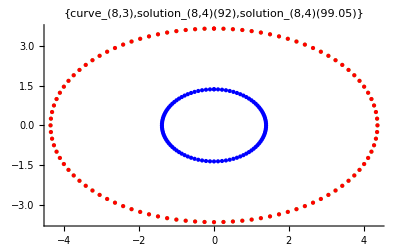

```mathematica
fgp[8,4,7.05]
```

```mathematica
edp[8,4,40]
```

u-Bestimmungsdauer: 20.0973

```mathematica
fit[8,4,3]
```

8. curve, 4. fit: length after flow = 8.65193 , length after fit = 8.65193 , derivation = 0.0000245808 %

8. curve, 5.evolution:   initial length = 8.65193 , length after flow = 2.84176 , time of evaluation = 0.056003

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

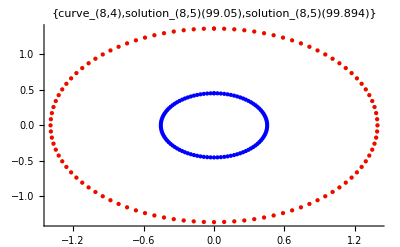

```mathematica
fgp[8,5,.844]
```

```mathematica
edp[8,5,20]
```

u-Bestimmungsdauer: 8.0405

```mathematica
fit[8,5,3]
```

8. curve, 5. fit: length after flow = 2.84176 , length after fit = 2.84176 , derivation = 5.41178×10^-6 %

8. curve, 6.evolution:   initial length = 2.84176 , length after flow = 0.687737 , time of evaluation = 0.064004

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

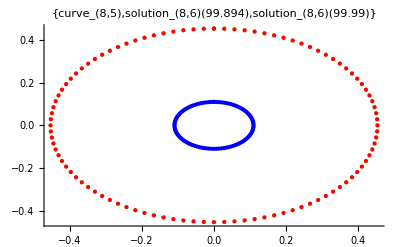

```mathematica
fgp[8,6,.096]
```

```mathematica
edp[8,6,20]
```

u-Bestimmungsdauer: 7.66848

```mathematica
fit[8,6,1]
```

8. curve, 6. fit: length after flow = 0.687737 , length after fit = 0.687736 , derivation = 0.0000760097 %

8. curve, 7.evolution:   initial length = 0.687736 , length after flow = 0.103079 , time of evaluation = 0.060004

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

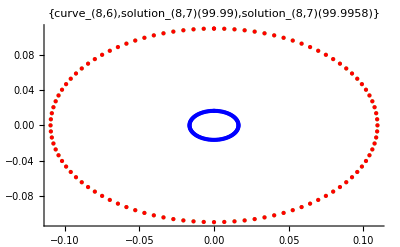

```mathematica
fgp[8,7,.0058]
```

```mathematica
edp[8,7,20]
```

u-Bestimmungsdauer: 6.48841

```mathematica
fit[8,7,1]
```

8. curve, 7. fit: length after flow = 0.103079 , length after fit = 0.103079 , derivation = 1.52451×10^-6 %

8. curve, 8.evolution:   initial length = 0.103079 , length after flow = 0.0297967 , time of evaluation = 0.036002

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

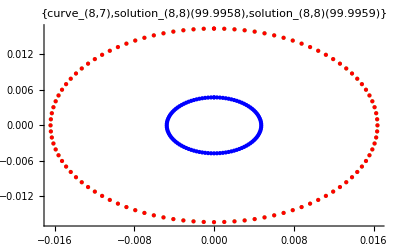

```mathematica
fgp[8,8,.00012]
```

#### curve 9

9. curve, 1.evolution: initial length = 96.2221 | length after flow = 89.532 | time of evaluation = 4.7763

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.9999951905

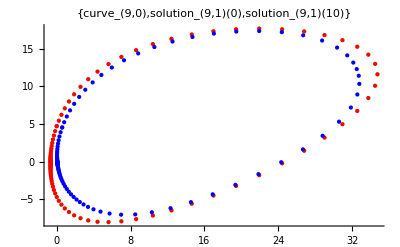

```mathematica
fgp[9,1,10]
```

```mathematica
edp[9,1,20]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {1.70569}. NIntegrate obtained 89.5319 and 0.000798287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {1.70569}. NIntegrate obtained 89.5319 and 0.000798287 for the integral and error estimates.

u-Bestimmungsdauer: 33.8501

```mathematica
edp[9,1,20,WorkingPrecision->12,PrecisionGoal->10]
```

u-Bestimmungsdauer: 25.3056

```mathematica
edp[9,1,20,WorkingPrecision->12,PrecisionGoal->6]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {1.38657480775}. NIntegrate obtained 89.5321505495 and 0.000914616507933 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {1.3865748078}. NIntegrate obtained 89.53215055 and 0.000914616507956 for the integral and error estimates.

u-Bestimmungsdauer: 25.2136

```mathematica
fit[9,1,10]
```

9. curve, 1. fit: length after flow = 85.7588 , length after fit = 85.7587 , derivation = 0.0000885623 %

9. curve, 2.evolution:   initial length = 85.7587 , length after flow = 25.1371 , time of evaluation = 0.104006

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999998

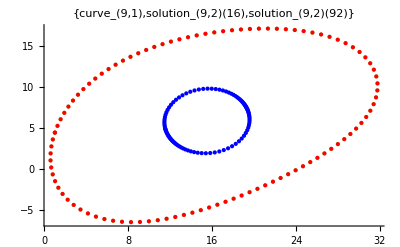

```mathematica
fgp[9,2,76]
```

```mathematica
edp[9,2,60]
```

u-Bestimmungsdauer: 38.9424

```mathematica
fit[9,2,3]
```

9. curve, 2. fit: length after flow = 25.1371 , length after fit = 25.1371 , derivation = 0.0000132531 %

9. curve, 3.evolution:   initial length = 25.1371 , length after flow = 7.87594 , time of evaluation = 0.048003

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999998

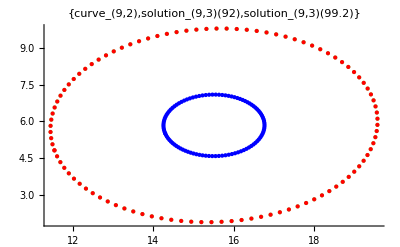

```mathematica
fgp[9,3,7.2]
```

```mathematica
edp[9,3,40]
```

u-Bestimmungsdauer: 17.7771

```mathematica
fit[9,3,4]
```

9. curve, 3. fit: length after flow = 7.87594 , length after fit = 7.87595 , derivation = 0.0000996978 %

9. curve, 4.evolution:   initial length = 7.87595 , length after flow = 2.5633 , time of evaluation = 0.056004

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999998

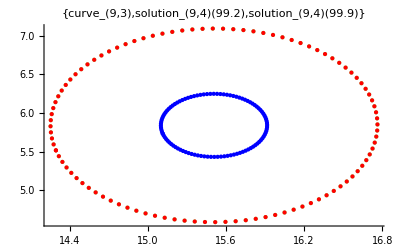

```mathematica
fgp[9,4,.7]
```

```mathematica
edp[9,4,40]
```

u-Bestimmungsdauer: 15.293

```mathematica
fit[9,4,3]
```

9. curve, 4. fit: length after flow = 2.5633 , length after fit = 2.5633 , derivation = 7.04378×10^-6 %

9. curve, 5.evolution:   initial length = 2.5633 , length after flow = 0.405933 , time of evaluation = 0.068005

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999998

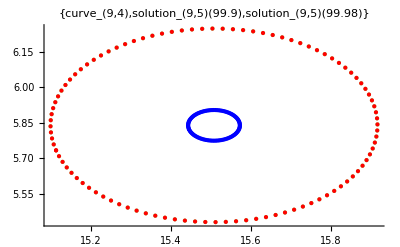

```mathematica
fgp[9,5,.08]
```

```mathematica
edp[9,5,36]
```

u-Bestimmungsdauer: 13.0928

```mathematica
fit[9,5,2]
```

9. curve, 5. fit: length after flow = 0.405933 , length after fit = 0.405933 , derivation = 5.2941×10^-6 %

9. curve, 6.evolution:   initial length = 0.405933 , length after flow = 0.278046 , time of evaluation = 0.028002

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999998

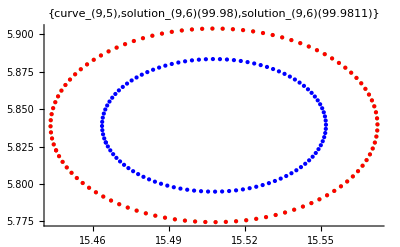

```mathematica
fgp[9,6,.0011]
```

```mathematica
edp[9,6,32]
```

u-Bestimmungsdauer: 9.83661

```mathematica
fit[9,6,1]
```

9. curve, 6. fit: length after flow = 0.278046 , length after fit = 0.278046 , derivation = 2.57936×10^-6 %

9. curve, 7.evolution:   initial length = 0.278046 , length after flow = 0.174131 , time of evaluation = 0.036002

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999998

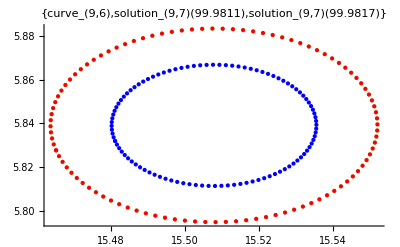

```mathematica
fgp[9,7,.00059]
```

```mathematica
edp[9,7,28]
```

u-Bestimmungsdauer: 9.6166

```mathematica
fit[9,7,1]
```

9. curve, 7. fit: length after flow = 0.174131 , length after fit = 0.174131 , derivation = 0.0000366266 %

9. curve, 8.evolution:   initial length = 0.174131 , length after flow = 0.11139 , time of evaluation = 0.036002

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999998

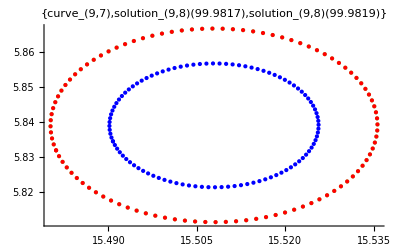

```mathematica
fgp[9,8,.000225]
```

```mathematica
edp[9,8,24]
```

u-Bestimmungsdauer: 8.13651

```mathematica
fit[9,8,1]
```

9. curve, 8. fit: length after flow = 0.11139 , length after fit = 0.11139 , derivation = 0.0000667363 %

9. curve, 9.evolution:   initial length = 0.11139 , length after flow = 0.0723957 , time of evaluation = 0.020001

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999998

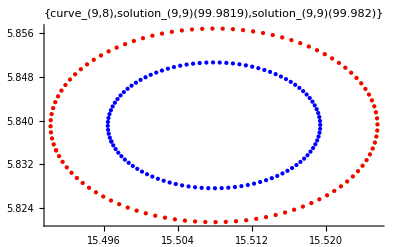

```mathematica
fgp[9,9,.00009]
```

```mathematica
edp[9,9,24]
```

u-Bestimmungsdauer: 8.66054

```mathematica
fit[9,9,1]
```

9. curve, 9. fit: length after flow = 0.0723957 , length after fit = 0.0723959 , derivation = 0.000361657 %

9. curve, 10.evolution:   initial length = 0.0723959 , length after flow = 0.0474753 , time of evaluation = 0.036002

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999998

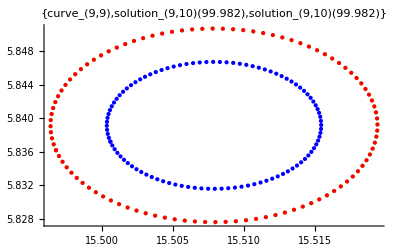

```mathematica
fgp[9,10,.0000372]
```

```mathematica
edp[9,10,24]
```

u-Bestimmungsdauer: 8.0085

```mathematica
fit[9,10,1]
```

9. curve, 10. fit: length after flow = 0.0474753 , length after fit = 0.0474753 , derivation = 0.0000217987 %

9. curve, 11.evolution:   initial length = 0.0474753 , length after flow = 0.0234166 , time of evaluation = 0.036002

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999998

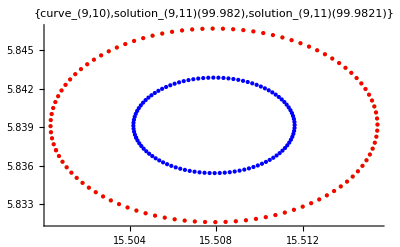

```mathematica
fgp[9,11,.0000210]
```

#### curve 10

10. curve, 1.evolution:   initial length = 95.9197 , length after flow = 45.3638 , time of evaluation = 0.200013

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999994

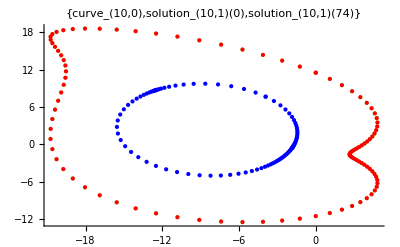

```mathematica
fgp[10,1,74]
```

```mathematica
edp[10,1,100]
```

u-Bestimmungsdauer: 99.9862

```mathematica
fit[10,1,9]
```

10. curve, 1. fit: length after flow = 45.3638 , length after fit = 45.3638 , derivation = 0.0000352325 %

10. curve, 2.evolution:   initial length = 45.3638 , length after flow = 6.82633 , time of evaluation = 0.084005

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999994

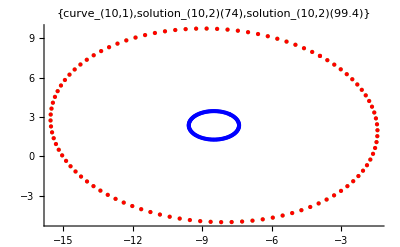

```mathematica
fgp[10,2,25.4]
```

```mathematica
edp[10,2,40]
```

u-Bestimmungsdauer: 19.7612

```mathematica
fit[10,2,3]
```

10. curve, 2. fit: length after flow = 6.82633 , length after fit = 6.82633 , derivation = 0.0000310846 %

10. curve, 3.evolution:   initial length = 6.82633 , length after flow = 3.00212 , time of evaluation = 0.044003

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999994

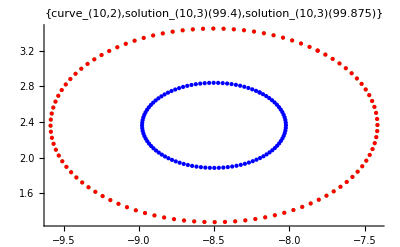

```mathematica
fgp[10,3,.475]
```

```mathematica
edp[10,3,36]
```

u-Bestimmungsdauer: 13.6569

```mathematica
fit[10,3,3]
```

10. curve, 3. fit: length after flow = 3.00212 , length after fit = 3.00212 , derivation = 0.0000521693 %

10. curve, 4.evolution:   initial length = 3.00212 , length after flow = 0.541486 , time of evaluation = 0.084006

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999994

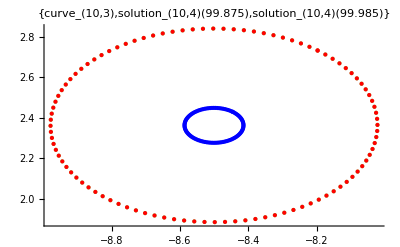

```mathematica
fgp[10,4,.11]
```

```mathematica
edp[10,4,36]
```

u-Bestimmungsdauer: 12.9408

```mathematica
fit[10,4,1]
```

10. curve, 4. fit: length after flow = 0.541486 , length after fit = 0.541486 , derivation = 0.0000222961 %

10. curve, 5.evolution:   initial length = 0.541486 , length after flow = 0.280472 , time of evaluation = 0.036003

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999994

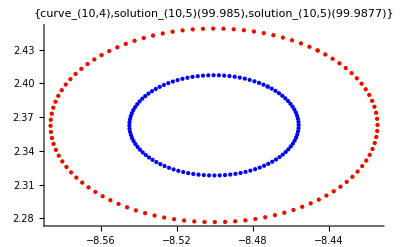

```mathematica
fgp[10,5,.0027]
```

```mathematica
edp[10,5,36]
```

u-Bestimmungsdauer: 10.9407

```mathematica
fit[10,5,1]
```

10. curve, 5. fit: length after flow = 0.280472 , length after fit = 0.280472 , derivation = 0.0000283767 %

10. curve, 6.evolution:   initial length = 0.280472 , length after flow = 0.180264 , time of evaluation = 0.036002

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999994

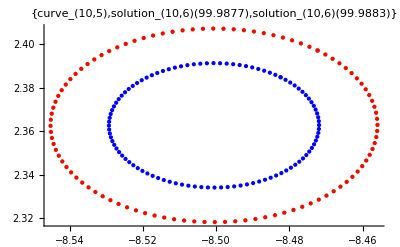

```mathematica
fgp[10,6,.00058]
```

```mathematica
edp[10,6,32]
```

u-Bestimmungsdauer: 10.5487

```mathematica
fit[10,6,1]
```

10. curve, 6. fit: length after flow = 0.180264 , length after fit = 0.180264 , derivation = 8.157×10^-7 %

10. curve, 7.evolution:   initial length = 0.180264 , length after flow = 0.0671057 , time of evaluation = 0.032002

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999994

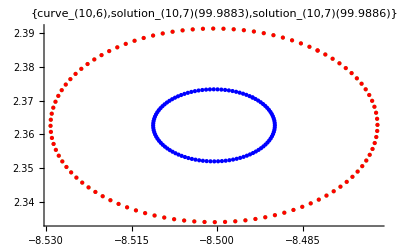

```mathematica
fgp[10,7,.00035]
```

```mathematica
edp[10,7,36]
```

u-Bestimmungsdauer: 12.2888

```mathematica
fit[10,7,1]
```

10. curve, 7. fit: length after flow = 0.0671057 , length after fit = 0.0671057 , derivation = 0.0000321958 %

10. curve, 8.evolution:   initial length = 0.0671057 , length after flow = 0.0448646 , time of evaluation = 0.036002

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999994

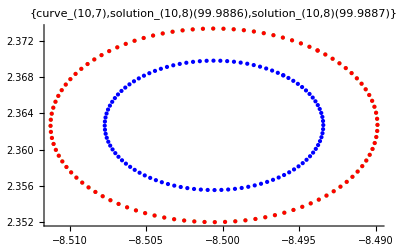

```mathematica
fgp[10,8,.0000313]
```

```mathematica
edp[10,8,36]
```

u-Bestimmungsdauer: 12.0048

```mathematica
fit[10,8,1]
```

10. curve, 8. fit: length after flow = 0.0448646 , length after fit = 0.0448646 , derivation = 8.07193×10^-6 %

10. curve, 9.evolution:   initial length = 0.0448646 , length after flow = 0.0323036 , time of evaluation = 0.044003

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.99999994

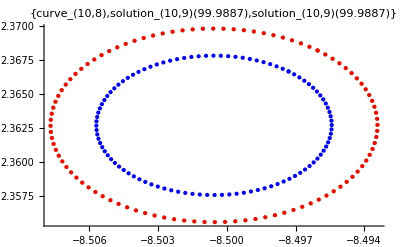

```mathematica
fgp[10,9,.0000122]
```

#### curve 11

11. curve, 1.evolution: initial length = 102.49 | length after flow = 79.9544 | time of evaluation = 1.44809

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 99.9999999747

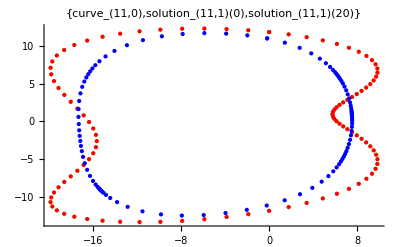

```mathematica
fgp[11,1,20]
```

```mathematica
Options[NIntegrate`GlobalAdaptive]
```

{Method→Automatic,MinRecursion→0,MaxRecursion→9,MaxPoints→∞,SingularityDepth→Automatic,MaxErrorIncreases→Automatic,SingularityHandler→Automatic,SymbolicProcessing→Automatic}

```mathematica
edp[11,1,5]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

u-Bestimmungsdauer: 7.04844

```mathematica
edp[11,1,5,Method->"LocalAdaptive"]
```

u-Bestimmungsdauer: 7.76849

```mathematica
edp[11,1,5,Method->"MultiPeriodic"]
```

Part::partw: Part 1 of {} does not exist.

Part::pspec: Part specification {} ⟦ 1 ⟧["Dimension"] is neither an integer nor a list of integers.

Part::partw: Part 1 of {} does not exist.

Part::pspec: Part specification {} ⟦ 1 ⟧["Dimension"] is neither an integer nor a list of integers.

General::stop: Further output of Part :: "pspec" will be suppressed during this calculation.

NIntegrate::intpm: Positive machine-size integer expected at position 2 in "Vector" → {{}, « 9 », « 2 »} ⟦ {} ⟦ 1 ⟧["Dimension"], 5, 3 ⟧.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 2 iterated refinements in "ArgumentNames"[] in the region NIntegrate`MultiPeriodicDump`topregion$2082326["Boundaries"]. NIntegrate obtained 0 and 0 for the integral and error estimates.

N::preclg: Requested precision 4\ MachinePrecision is larger than $MaxPrecision. Using current $MaxPrecision of 15.9546 instead. $MaxPrecision = Infinity specifies that any precision should be allowed.

Solve::tdep: The equations appear to involve the variables to be solved for in an essentially non-algebraic way.

N::preclg: Requested precision 4\ MachinePrecision is larger than $MaxPrecision. Using current $MaxPrecision of 15.9546 instead. $MaxPrecision = Infinity specifies that any precision should be allowed.

Solve::tdep: The equations appear to involve the variables to be solved for in an essentially non-algebraic way.

$Aborted

N::preclg: Requested precision 4\ MachinePrecision is larger than $MaxPrecision. Using current $MaxPrecision of 15.9546 instead. $MaxPrecision = Infinity specifies that any precision should be allowed.

General::stop: Further output of N :: "preclg" will be suppressed during this calculation.

$Aborted

```mathematica
edp[11,1,5,Method->"DoubleExponential"]
```

u-Bestimmungsdauer: 13.5848

```mathematica
edp[11,1,5,Method->"MonteCarlo"]
```

FindRoot::brmp: The root has been bracketed as closely as possible with machine precision but the function value exceeds the absolute tolerance 1.05367×10^-8.

$Aborted

```mathematica
edp[11,1,5,Method->"AdaptiveMonteCarlo"]
```

FindRoot::brmp: The root has been bracketed as closely as possible with machine precision but the function value exceeds the absolute tolerance 1.05367×10^-8.

$Aborted

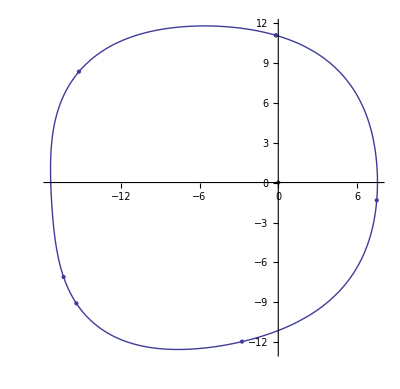

```mathematica
Show[equiplot[11,1],ListPlot[{{x[4.01299,Subscript[te, 11,1]],y[4.01299,Subscript[te, 11,1]]}/.Subscript[solution, 11,1][[1]],{0,0}},PlotStyle->PointSize[Large]]]
```

```mathematica
edp[11,1,20,WorkingPrecision->13]
```

u-Bestimmungsdauer: 25.5576

```mathematica
fit[11,1,9]
```

11. curve, 1. fit: length after flow = 45.3012 , length after fit = 45.3012 , derivation = 0.000025093 %

11. curve, 2.evolution:   initial length = 45.3012 , length after flow = 4.66215 , time of evaluation = 0.100007

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

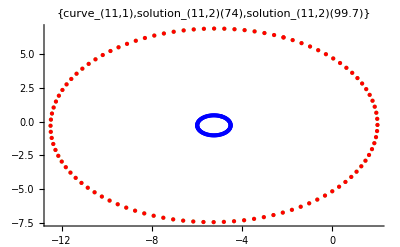

```mathematica
fgp[11,2,25.7]
```

```mathematica
edp[11,2,44]
```

u-Bestimmungsdauer: 19.8612

```mathematica
fit[11,2,3]
```

11. curve, 2. fit: length after flow = 4.66215 , length after fit = 4.66215 , derivation = 0.0000251591 %

11. curve, 3.evolution:   initial length = 4.66215 , length after flow = 0.607947 , time of evaluation = 0.068005

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

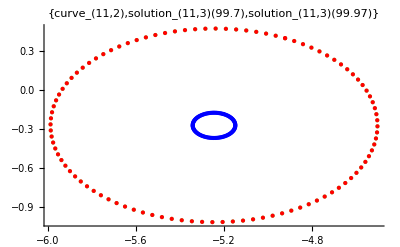

```mathematica
fgp[11,3,.27]
```

```mathematica
edp[11,3,36]
```

u-Bestimmungsdauer: 13.0608

```mathematica
fit[11,3,1]
```

11. curve, 3. fit: length after flow = 0.607947 , length after fit = 0.607947 , derivation = 6.19539×10^-7 %

11. curve, 4.evolution:   initial length = 0.607947 , length after flow = 0.289425 , time of evaluation = 0.036002

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

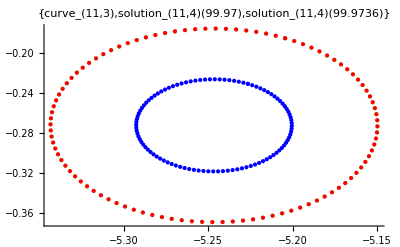

```mathematica
fgp[11,4,.0036]
```

```mathematica
edp[11,4,32]
```

u-Bestimmungsdauer: 10.2966

```mathematica
fit[11,4,1]
```

11. curve, 4. fit: length after flow = 0.289425 , length after fit = 0.289425 , derivation = 2.10592×10^-6 %

11. curve, 5.evolution:   initial length = 0.289425 , length after flow = 0.060651 , time of evaluation = 0.056004

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

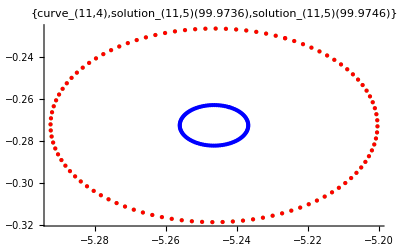

```mathematica
fgp[11,5,.001]
```

```mathematica
edp[11,5,32]
```

u-Bestimmungsdauer: 10.4567

```mathematica
fit[11,5,1]
```

11. curve, 5. fit: length after flow = 0.060651 , length after fit = 0.060651 , derivation = 0.0000235768 %

11. curve, 6.evolution:   initial length = 0.060651 , length after flow = 0.0331171 , time of evaluation = 0.032002

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

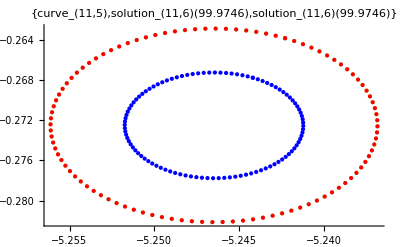

```mathematica
fgp[11,6,.0000325]
```

```mathematica
edp[11,6,28]
```

u-Bestimmungsdauer: 8.74455

```mathematica
fit[11,6,1]
```

11. curve, 6. fit: length after flow = 0.0331171 , length after fit = 0.0331171 , derivation = 7.37294×10^-6 %

11. curve, 7.evolution:   initial length = 0.0331171 , length after flow = 0.013891 , time of evaluation = 0.032002

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

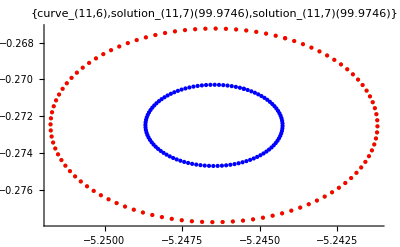

```mathematica
fgp[11,7,.0000113]
```

```mathematica
edp[11,7,24]
```

u-Bestimmungsdauer: 8.40452

```mathematica
fit[11,7,1]
```

11. curve, 7. fit: length after flow = 0.013891 , length after fit = 0.0138911 , derivation = 0.0000997927 %

11. curve, 8.evolution:   initial length = 0.0138911 , length after flow = 0.00984213 , time of evaluation = 0.036003

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

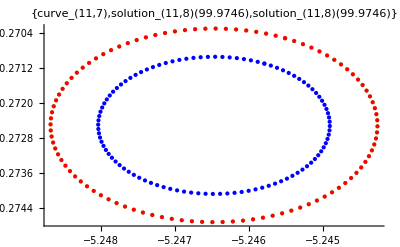

```mathematica
fgp[11,8,.0000012]
```

#### curve 12

12. curve, 1.evolution:   initial length = 92.5769 , length after flow = 30.7603 , time of evaluation = 0.112006

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

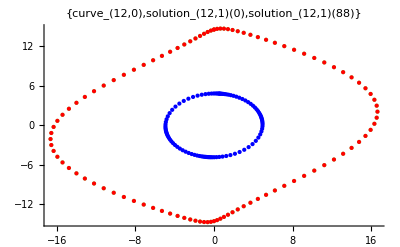

```mathematica
fgp[12,1,88]
```

```mathematica
edp[12,1,80]
```

u-Bestimmungsdauer: 64.556

```mathematica
fit[12,1,5]
```

12. curve, 1. fit: length after flow = 30.7603 , length after fit = 30.7603 , derivation = 4.90481×10^-6 %

12. curve, 2.evolution:   initial length = 30.7603 , length after flow = 5.35934 , time of evaluation = 0.068004

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

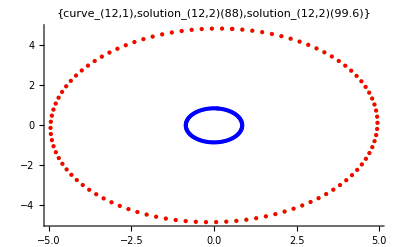

```mathematica
fgp[12,2,11.6]
```

```mathematica
edp[12,2,44]
```

u-Bestimmungsdauer: 20.2893

```mathematica
fit[12,2,3]
```

12. curve, 2. fit: length after flow = 5.35934 , length after fit = 5.35934 , derivation = 1.45362×10^-6 %

12. curve, 3.evolution:   initial length = 5.35934 , length after flow = 1.34781 , time of evaluation = 0.068004

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

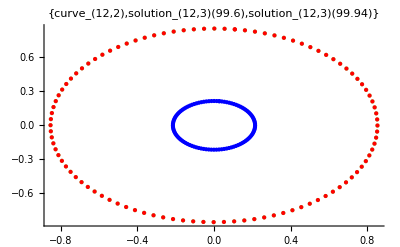

```mathematica
fgp[12,3,.34]
```

```mathematica
edp[12,3,40]
```

u-Bestimmungsdauer: 15.377

```mathematica
fit[12,3,3]
```

12. curve, 3. fit: length after flow = 1.34781 , length after fit = 1.34781 , derivation = 6.10066×10^-6 %

12. curve, 4.evolution:   initial length = 1.34781 , length after flow = 0.481356 , time of evaluation = 0.052003

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

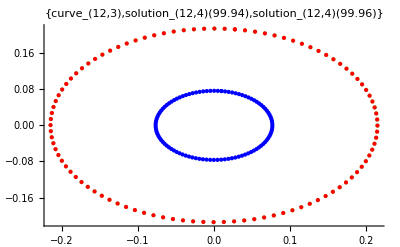

```mathematica
fgp[12,4,.02]
```

```mathematica
edp[12,4,40]
```

u-Bestimmungsdauer: 13.3808

```mathematica
fit[12,4,3]
```

12. curve, 4. fit: length after flow = 0.481356 , length after fit = 0.481356 , derivation = 0.0000197692 %

12. curve, 5.evolution:   initial length = 0.481356 , length after flow = 0.0887036 , time of evaluation = 0.060004

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

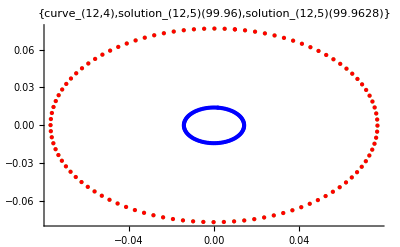

```mathematica
fgp[12,5,.0028]
```

```mathematica
edp[12,5,36]
```

u-Bestimmungsdauer: 11.1647

```mathematica
fit[12,5,1]
```

12. curve, 5. fit: length after flow = 0.0887036 , length after fit = 0.0887036 , derivation = 1.76879×10^-8 %

12. curve, 6.evolution:   initial length = 0.0887036 , length after flow = 0.0301442 , time of evaluation = 0.036002

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

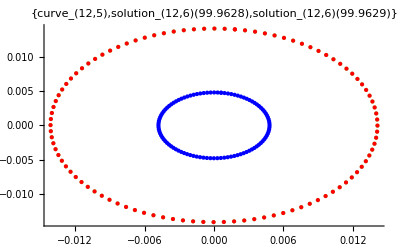

```mathematica
fgp[12,6,.000087]
```

```mathematica
edp[12,6,32]
```

u-Bestimmungsdauer: 10.1366

```mathematica
fit[12,6,1]
```

12. curve, 6. fit: length after flow = 0.0301442 , length after fit = 0.0301442 , derivation = 0.0000213974 %

12. curve, 7.evolution:   initial length = 0.0301442 , length after flow = 0.00954929 , time of evaluation = 0.032002

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

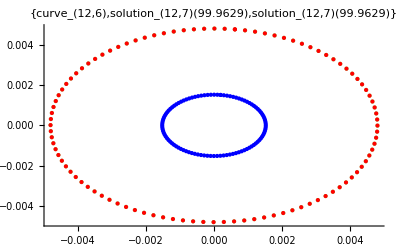

```mathematica
fgp[12,7,.0000102]
```

#### curve 13

13. curve, 1.evolution:   initial length = 165.853 , length after flow = 158.608 , time of evaluation = 0.028001

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

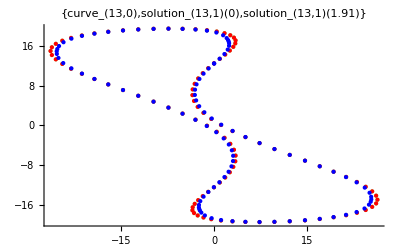

```mathematica
fgp[13,1,1.91,StartingPoints->100,MinPoints->100]
```

```mathematica
edp[13,1,200]
```

u-Bestimmungsdauer: 110.843

```mathematica
fit[13,1,17]
```

13. curve, 1. fit: length after flow = 158.608 , length after fit = 158.153 , derivation = 0.286471 %

13. curve, 2.evolution:   initial length = 158.153 , length after flow = 148.279 , time of evaluation = 0.060003

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

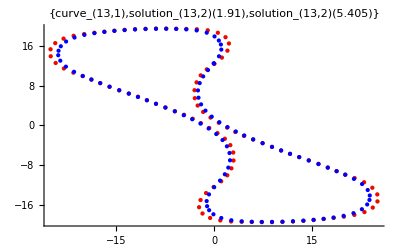

```mathematica
fgp[13,2,3.495]
```

```mathematica
edp[13,2,200]
```

u-Bestimmungsdauer: 80.8971

```mathematica
fit[13,2,17]
```

13. curve, 2. fit: length after flow = 148.279 , length after fit = 148.184 , derivation = 0.0640814 %

13. curve, 3.evolution:   initial length = 148.184 , length after flow = 86.1456 , time of evaluation = 0.140009

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

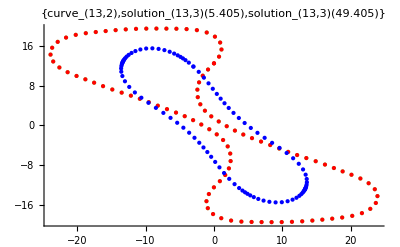

```mathematica
fgp[13,3,44]
```

```mathematica
edp[13,3,100]
```

u-Bestimmungsdauer: 73.5486

```mathematica
fit[13,3,12]
```

13. curve, 3. fit: length after flow = 86.1456 , length after fit = 86.1454 , derivation = 0.000297617 %

13. curve, 4.evolution:   initial length = 86.1454 , length after flow = 56.9184 , time of evaluation = 0.096006

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

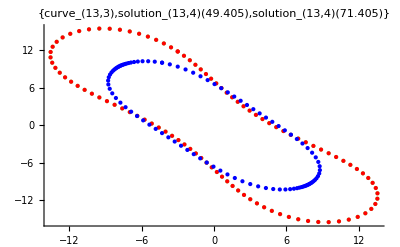

```mathematica
fgp[13,4,22]
```

```mathematica
edp[13,4,100]
```

u-Bestimmungsdauer: 56.4395

```mathematica
fit[13,4,13]
```

13. curve, 4. fit: length after flow = 56.9184 , length after fit = 56.918 , derivation = 0.000795591 %

13. curve, 5.evolution:   initial length = 56.918 , length after flow = 33.2324 , time of evaluation = 0.104006

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

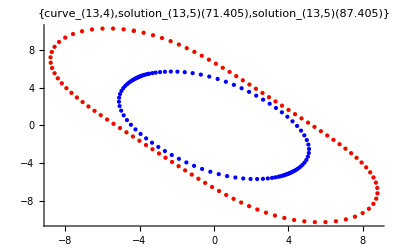

```mathematica
fgp[13,5,16]
```

```mathematica
edp[13,5,80]
```

u-Bestimmungsdauer: 46.8869

```mathematica
fit[13,5,8]
```

13. curve, 5. fit: length after flow = 33.2324 , length after fit = 33.2326 , derivation = 0.000543459 %

13. curve, 6.evolution:   initial length = 33.2326 , length after flow = 14.2937 , time of evaluation = 0.076005

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

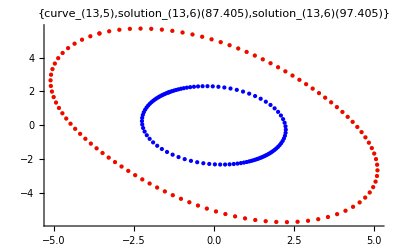

```mathematica
fgp[13,6,10]
```

```mathematica
edp[13,6,60]
```

u-Bestimmungsdauer: 33.2901

```mathematica
fit[13,6,4]
```

13. curve, 6. fit: length after flow = 14.2937 , length after fit = 14.2937 , derivation = 0.000391114 %

13. curve, 7.evolution:   initial length = 14.2937 , length after flow = 3.67513 , time of evaluation = 0.064004

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

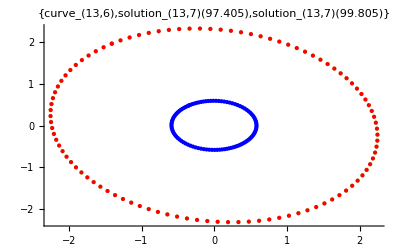

```mathematica
fgp[13,7,2.4]
```

```mathematica
edp[13,7,40]
```

u-Bestimmungsdauer: 19.2292

```mathematica
fit[13,7,3]
```

13. curve, 7. fit: length after flow = 3.67513 , length after fit = 3.67513 , derivation = 8.08699×10^-7 %

13. curve, 8.evolution:   initial length = 3.67513 , length after flow = 1.63234 , time of evaluation = 0.044003

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

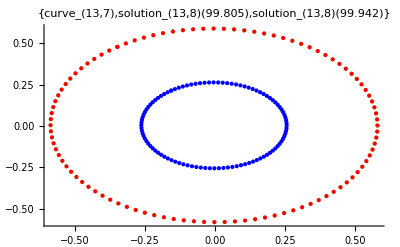

```mathematica
fgp[13,8,.137]
```

```mathematica
edp[13,8,24]
```

u-Bestimmungsdauer: 9.02056

```mathematica
fit[13,8,3]
```

13. curve, 8. fit: length after flow = 1.63234 , length after fit = 1.63234 , derivation = 0.0000166764 %

13. curve, 9.evolution:   initial length = 1.63234 , length after flow = 1.27891 , time of evaluation = 0.036002

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

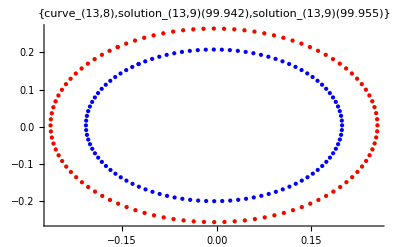

```mathematica
fgp[13,9,.013]
```

```mathematica
edp[13,9,24]
```

u-Bestimmungsdauer: 8.0205

```mathematica
fit[13,9,1]
```

13. curve, 9. fit: length after flow = 1.27891 , length after fit = 1.27892 , derivation = 0.000433247 %

13. curve, 10.evolution:   initial length = 1.27892 , length after flow = 1.23173 , time of evaluation = 0.024002

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

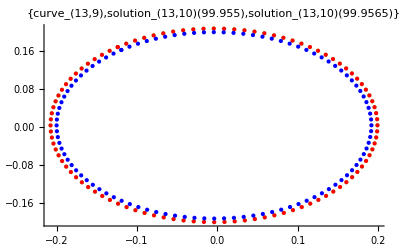

```mathematica
fgp[13,10,.0015]
```

```mathematica
edp[13,10,24]
```

u-Bestimmungsdauer: 7.08044

```mathematica
fit[13,10,1]
```

13. curve, 10. fit: length after flow = 1.23173 , length after fit = 1.23173 , derivation = 0.000306724 %

13. curve, 11.evolution:   initial length = 1.23173 , length after flow = 1.23029 , time of evaluation = 0.016001

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

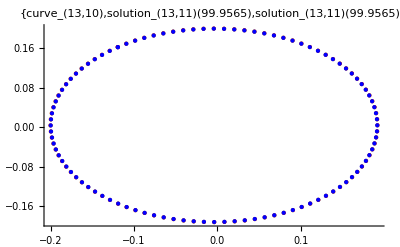

```mathematica
fgp[13,11,.000045]
```

```mathematica
edp[13,11,24]
```

u-Bestimmungsdauer: 6.82843

```mathematica
fit[13,11,1]
```

13. curve, 11. fit: length after flow = 1.23029 , length after fit = 1.23029 , derivation = 0.000233534 %

13. curve, 12.evolution:   initial length = 1.23029 , length after flow = 1.22955 , time of evaluation = 0.016001

gridpoints used by NUMOL: 100, endtime from initialcurve = 100., endtime from solution = 100.

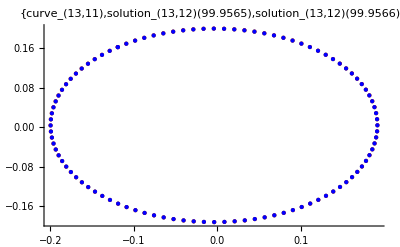

```mathematica
fgp[13,12,.000023]
```

### evolution plot,isoperimetric fit

#### evolution plots: 3D, length, area, isoperimetric ratio

```mathematica
noc=13;
Table[slength[num,Subscript[stepstop, num]],{num,1,noc}]
```

{0.0315413,0.0109139,0.0470811,0.0298145,0.0287676,0.0118436,0.0164459,0.0297967,0.0234166,0.0323036,0.00984213,0.00954929,0.0144087}

```mathematica
Table[evoplot[num],{num,1,noc}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

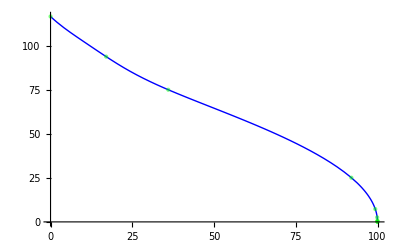
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Subscript[lplot, num],{num,1,noc}]
```

```mathematica
Table[Subscript[isoplot, num],{num,1,noc}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### isoperimetric ratio fit

```mathematica
Table[N[Subscript[ao, num],5],{num,1,noc}]
```

{628.319,628.319,628.319,628.319,628.319,628.319,628.319,628.319,628.319,628.319,628.319,628.319,628.319}

```mathematica
areao=Subscript[ao, 1]
```

628.319

```mathematica
N[Subscript[ao, 1],5]
```

628.319

```mathematica
isofit[num_,datapts_,order_]:=Fit[Join[Table[{i/datapts Subscript[te, num,Subscript[stepstop, num]],Subscript[length, num][i/datapts Subscript[te, num,Subscript[stepstop, num]]]^2/(areao-(2π  i/datapts Subscript[te, num,Subscript[stepstop, num]]))},{i,0,datapts}],{{100,4π}}],Table[t^i,{i,0,order}],t];
Subscript[l, num_]:=Sqrt[(Subscript[iso, num])(Subscript[ao, num]-2π t)];
Do[Subscript[iso, num]=isofit[num,50,10],{num,1,2}]
```

```mathematica
Plot[{Subscript[area, 1][t],Subscript[ao, 1]-2π t,areao},{t,0,Subscript[te, 1,Subscript[stepstop, 1]]}]
```

-Graphics-

```mathematica
Plot[{Table[Subscript[iso, num],{num,1,2}]},{t,0,100},PlotRange->Full]
```

-Graphics-

```mathematica
Plot[Table[Subscript[l, num],{num,1,noc}],{t,0,100}]
```

-Graphics-

### partition function

```mathematica
z=Sum[Exp[-Subscript[iso, num](1+c[t]/Subscript[l, num])],{num,1,noc}];
pde=Evaluate[D[z, t]] ==0;
bc=Sum[Subscript[l, num] Exp[-Subscript[iso, num](1+c[t]/Subscript[l, num])] /.t->0,{num,1,noc}]/(z/.t->0)==Sum[Subscript[l, num]/.t->0,{num,1,noc}]/noc;
```

```mathematica
Sum[Subscript[l, num]/.t->0,{num,1,noc}]/noc
```

116.952

```mathematica
co=c[0]/.FindRoot[bc,{c[0],-500}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

4510.

```mathematica
zsol=NDSolve[{pde,c[0]==co},c,{t,0,99.9}]
```

$Aborted

```mathematica
z/.zsol/.t->0
```

{7.85688×10^9}

```mathematica
zo=z/.zsol[[1]]/.t->0
```

7.85688×10^9

```mathematica
Plot[(c[t]/.zsol[[1]])/zo,{t,0,99.9}]
```

-Graphics-

```mathematica
zoo=Sum[Exp[-Subscript[iso, num](1+1/Subscript[l, num])],{num,1,noc}]/.t->0
```

3.24293×10^-7

```mathematica
Plot[{(z/.zsol[[1]])/zo,Sum[Exp[-Subscript[iso, num](1+1/Subscript[l, num])]/zoo,{num,1,noc}]},{t,0,99.9}]
```

-Graphics-